## IGP system with adaptive predator-specific defense and introduced predator

## First replicate Nakazawa by omitting ρ and setting f_i to published values

Define Model

```mathematica
Clear["Global`*"]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional reponse of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resourse *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fP));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(*fitness is defined as the per capita growth rate of the resource*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) -  aPR P (1 - eP fP);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
```

eΝ v (-aΝR (eΝ-1) fΝ Ν-aPR eP fP P+c0 r (eΝ+eP-1))

-eP v (aΝR eΝ fΝ Ν+aPR (eP-1) fP P-c0 r (eΝ+eP-1))

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1.,k-> 5., c0->0.25, fP->0.5,fΝ->0.5,  aPR-> 0.25, aPΝ -> 1., aΝR -> 1., bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1.};
kpars = Delete[pars, 2]
```

{r→1.,c0→0.25,fP→0.5,fΝ→0.5,aPR→0.25,aPΝ→1.,aΝR→1.,bPΝ→0.5,bΝR→0.5,bPR→0.5,mP→0.5,mΝ→0.5,v→1.}

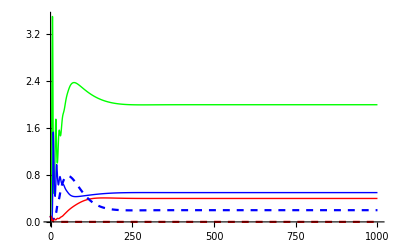

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.pars},{R,Ν, P, eΝ, eP},{t,0,1000}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,1000}, PlotStyle-> cols]
```

### Manipulate across gradients of k and aPΝ

```mathematica
(*Huzzah! Adaptive predator-specific model works! Not only do the stable/unstable and coexistence dynamics exactly match Nakazawa Fig. 3 but the effort variables  somehow (automatically) sum to less than 1 across all ranges of parameter space (something that I was worried about needing to constrain explicitely)*)
```

```mathematica
kaPΝpars = {r-> 1, c0->0.25, fP->0.5,fΝ->0.5,  aPR-> 0.25,aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1}
```

{r→1,c0→0.25,fP→0.5,fΝ→0.5,aPR→0.25,aΝR→1,bPΝ→0.5,bΝR→0.5,bPR→0.5,mP→0.5,mΝ→0.5,v→1}

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[kaPΝpars,{k->κ,aPΝ->α}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{κ,5,"k"},0,20},{{α,1,"aPΝ"},0,4}]
```

Solve for equilibria and plot domains of coexistence

### Equilibria

```mathematica
equilRNP=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,deΝdt == 0,dPdt==0, dePdt==0},{R,Ν, eΝ,P, eP}]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
equil//TableForm
```

R→0 | Ν→0 | eΝ→1-eP | P→0 | 
R→-(c0-1) k r | Ν→0 | eΝ→1-eP | P→0 | 
R→k r | Ν→0 | eΝ→0 | P→0 | eP→0
R→(k (aΝR (fΝ-1) mP+bPΝ (aPR mΝ-aPΝ (c0-1) r)))/(aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR (c0-1) k r+mP)-aPR k (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | eΝ→1 | P→(aΝR (fΝ-1) k (-aΝR bΝR (fΝ-1) mP+aPΝ bΝR bPΝ (c0-1) r-aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | eP→0
R→(aΝR fΝ mP-aPΝ bPΝ c0 r)/(aΝR aPR bPR fΝ) | Ν→(c0 r)/(aΝR fΝ) | eΝ→(aΝR fΝ (aPΝ mP+aPR k (aΝR bΝR mP-aPR bPR mΝ))-aPΝ r (aPΝ bPΝ c0+aΝR aPR k (bΝR bPΝ c0+bPR (fΝ-c0))))/(aΝR aPR bΝR fΝ k (aΝR fΝ mP-aPΝ bPΝ c0 r)) | P→(-aΝR fΝ mP+aPΝ bPΝ c0 r+aΝR aPR bPR k r (fΝ-c0))/(aΝR aPR^2 bPR fΝ k) | eP→0
R→mP/(aPR bPR) | Ν→0 | eΝ→0 | P→(aPR r-mP/(bPR k))/aPR^2 | eP→0
R→0 | Ν→0 | eΝ→1 | P→0 | eP→0
R→-(c0-1) k r | Ν→0 | eΝ→1 | P→0 | eP→0
R→mP/(aPR bPR) | Ν→0 | eΝ→1 | P→-(aPR bPR (c0-1) k r+mP)/(aPR^2 bPR k) | eP→0
R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | eΝ→0 | P→(aPR bPR (c0-1) (fP-1) k r-mP)/(aPR^2 bPR (fP-1)^2 k) | eP→1
R→-(c0-1) k r | Ν→0 | eΝ→mP/(aPR bPR fP k r-aPR bPR c0 fP k r)-1/fP+1 | P→0 | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
R→(k r (fP-c0))/fP | Ν→0 | eΝ→0 | P→(c0 r)/(aPR fP) | eP→mP/(aPR bPR c0 k r-aPR bPR fP k r)+1/fP
R→k r (1-(c0 (fΝ+fP))/(fΝ fP)) | Ν→(c0 r)/(aΝR fΝ) | eΝ→(aPΝ c0 fΝ r+aΝR aPR bΝR k r (c0 (fΝ+fP)-fΝ fP)+aPR fΝ fP mΝ)/(aΝR aPR bΝR fΝ k r (c0 (fΝ+fP)-fΝ fP)) | P→(c0 r)/(aPR fP) | eP→(aΝR fΝ fP mP-aPΝ bPΝ c0 fP r+aΝR aPR bPR k r (c0 (fΝ+fP)-fΝ fP))/(aΝR aPR bPR fP k r (c0 (fΝ+fP)-fΝ fP))
R→(k (-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ)-((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))/(aPΝ fΝ fP (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (fΝ-fΝ fP+fP)^2) | Ν→(aΝR aPR bΝR bPR (c0-1) fP k r ((fΝ-1) fP-fΝ)-fP (aΝR bΝR fΝ mP+aPR bPR fP mΝ))/(aΝR (aPΝ fΝ fP (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (fΝ-fΝ fP+fP)^2)) | eΝ→(aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR mP+aPR bPR (fP-1) mΝ)-aPΝ (aΝR fΝ mP+aPR bPΝ fP mΝ)-aΝR aPΝ aPR (c0-1) k r (bΝR bPΝ fP-bPR fΝ (fP-1)))/(aΝR aPR k (aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ)+((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))) | P→-(fΝ (aΝR bΝR (fΝ mP-aPR bPR (c0-1) k r ((fΝ-1) fP-fΝ))+aPR bPR fP mΝ))/(aPR (aPΝ fΝ fP (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (fΝ-fΝ fP+fP)^2)) | eP→(aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ (aΝR fΝ mP-aΝR aPR (c0-1) k r (bΝR bPΝ (fΝ-1) fP-bPR fΝ)+aPR bPΝ fP mΝ))/(aΝR aPR k (aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ)+((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))
R→-(k (aΝR mP+aPΝ bPΝ (c0-1) r+aPR bPΝ (fP-1) mΝ))/(aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR k r (c0 (-fP)+c0+fP-1)+mP)-aPR (fP-1) k (aΝR bΝR mP+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | eΝ→0 | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bΝR bPΝ (c0-1) r+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | eP→1
R→(aPΝ c0 r+aPR fP mΝ)/(aΝR aPR bΝR fP) | Ν→(-aPΝ c0 r+aΝR aPR bΝR k r (fP-c0)-aPR fP mΝ)/(aΝR^2 aPR bΝR fP k) | eΝ→0 | P→(c0 r)/(aPR fP) | eP→(aPΝ r (aΝR aPR k (bΝR bPΝ (fP-c0)+bPR c0)-aPΝ bPΝ c0)+aPR fP (aΝR k (aPR bPR mΝ-aΝR bΝR mP)-aPΝ bPΝ mΝ))/(aΝR aPR bPR fP k (aPΝ c0 r+aPR fP mΝ))
R→mΝ/(aΝR bΝR) | Ν→(aΝR r-mΝ/(bΝR k))/aΝR^2 | eΝ→0 | P→0 | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→1
R→-(c0-1) k r | Ν→0 | eΝ→0 | P→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→-(aΝR bΝR (c0-1) k r+mΝ)/(aΝR^2 bΝR k) | eΝ→0 | P→0 | eP→1
R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(aΝR bΝR (c0-1) (fΝ-1) k r-mΝ)/(aΝR^2 bΝR (fΝ-1)^2 k) | eΝ→1 | P→0 | eP→0
R→-(c0-1) k r | Ν→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | P→0 | eP→mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)-1/fΝ+1
R→(k r (fΝ-c0))/fΝ | Ν→(c0 r)/(aΝR fΝ) | eΝ→mΝ/(aΝR bΝR c0 k r-aΝR bΝR fΝ k r)+1/fΝ | P→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | eΝ→1 | P→-mΝ/aPΝ | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | eΝ→0 | P→-mΝ/aPΝ | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | eΝ→0 | P→-mΝ/aPΝ | eP→1
R→(k (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | eΝ→0 | P→(aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→0

```mathematica
FullSimplify[equil[[17, 2,  2]]]
```

(aΝR r-mΝ/(bΝR k))/aΝR^2

```mathematica
equil/.kpars//TableForm
```

Power::infy: Infinite expression TraditionalForm`1/0. encountered.

R→0 | Ν→0 | eΝ→1-eP | P→0 | 
R→0.75 k | Ν→0 | eΝ→1-eP | P→0 | 
R→1. k | Ν→0 | eΝ→0 | P→0 | eP→0
R→(0.1875 k)/(0.5-0.03125 k) | Ν→(1. (1. (0.5-0.09375 k)+0.015625 k))/(0.5-0.03125 k) | eΝ→1 | P→(1. (0.0625 k-0.25))/(0.5-0.03125 k) | eP→0
R→2. | Ν→0.5 | eΝ→(128. (0.5 (0.046875 k+0.5)-1. (0.046875 k+0.125)))/k | P→(64. (0.03125 k-0.125))/k | eP→0
R→4. | Ν→0 | eΝ→0 | P→16. (0.25-1./k) | eP→0
R→0 | Ν→0 | eΝ→1 | P→0 | eP→0
R→0.75 k | Ν→0 | eΝ→1 | P→0 | eP→0
R→4. | Ν→0 | eΝ→1 | P→-(32. (0.5-0.09375 k))/k | eP→0
R→8. | Ν→0 | eΝ→0 | P→(128. (0.046875 k-0.5))/k | eP→1
R→0.75 k | Ν→0 | eΝ→10.6667/k-1. | P→0 | eP→2. (1-5.33333/k)
R→0.5 k | Ν→0 | eΝ→0 | P→2. | eP→2.-16./k
R→0. | Ν→0.5 | eΝ→ComplexInfinity | P→2. | eP→ComplexInfinity
R→(0.164063 k)/(0.0351563 k+0.0625) | Ν→(1. (0.0175781 k-0.078125))/(0.0351563 k+0.0625) | eΝ→-(24.381 (0.00585938 k-0.28125))/k | P→-(2. (0.5 (0.25-0.0703125 k)+0.03125))/(0.0351563 k+0.0625) | eP→-(24.381 (1. (0.28125-0.0585938 k)+0.0117188 k))/k
R→-(0.09375 k)/(0.5-0.03125 k) | Ν→(1. (1. (0.5-0.046875 k)+0.0273438 k))/(0.5-0.03125 k) | eΝ→0 | P→-(1. (0.03125 k+0.25))/(0.5-0.03125 k) | eP→1
R→5. | Ν→(16. (0.03125 k-0.3125))/k | eΝ→0 | P→2. | eP→(51.2 (0.125 (-0.1875 k-0.25)+1. (0.046875 k-0.125)))/k
R→1. | Ν→1. (1.-1./k) | eΝ→0 | P→0 | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→1
R→0.75 k | Ν→0 | eΝ→0 | P→0 | eP→1
R→1. | Ν→-(2. (0.5-0.375 k))/k | eΝ→0 | P→0 | eP→1
R→2. | Ν→(8. (0.1875 k-0.5))/k | eΝ→1 | P→0 | eP→0
R→0.75 k | Ν→0 | eΝ→2. (1-1.33333/k) | P→0 | eP→2.66667/k-1.
R→0.5 k | Ν→0.5 | eΝ→2.-4./k | P→0 | eP→0
R→0 | Ν→1. | eΝ→1 | P→-0.5 | eP→0
R→0 | Ν→1. | eΝ→0 | P→-0.5 | eP→0
R→0 | Ν→1. | eΝ→0 | P→-0.5 | eP→1
R→(0.0625 k)/(0.5-0.0625 k) | Ν→(1. (1. (0.5-0.125 k)+0.046875 k))/(0.5-0.0625 k) | eΝ→0 | P→(1. (0.0625 k-0.25))/(0.5-0.0625 k) | eP→0
R→0 | Ν→0 | eΝ→0 | P→0 | eP→0

```mathematica
ex = equil[[23, 3, 2]];
Solve[ex==0, k]
```

{{k→(fΝ mΝ)/(aΝR bΝR r (fΝ-c0))}}

Detemine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fΝ-1) | R (aΝR fΝ Ν-c0 r) | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aΝR bΝR Ν (1-eΝ fΝ) | aΝR bΝR R (1-eΝ fΝ)-aPΝ P-mΝ | -aΝR bΝR fΝ Ν R | -aPΝ Ν | 0
0 | -aΝR (eΝ-1) eΝ fΝ v | v (aΝR (1-2 eΝ) fΝ Ν-aPR eP fP P+c0 r (2 eΝ+eP-1)) | -aPR eΝ eP fP v | eΝ v (c0 r-aPR fP P)
aPR bPR P (1-eP fP) | aPΝ bPΝ P | 0 | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aΝR eΝ eP fΝ v | eP v (c0 r-aΝR fΝ Ν) | -aPR (eP-1) eP fP v | v (-aΝR eΝ fΝ Ν+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fΝ-1) | R (aΝR fΝ Ν-c0 r)
aΝR bΝR Ν (1-eΝ fΝ) | aΝR bΝR R (1-eΝ fΝ)-aPΝ P-mΝ | -aΝR bΝR fΝ Ν R
0 | -aΝR (eΝ-1) eΝ fΝ v | v (aΝR (1-2 eΝ) fΝ Ν-aPR eP fP P+c0 r (2 eΝ+eP-1)))

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aPR bPR P (1-eP fP) | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aPR (eP-1) eP fP v | v (-aΝR eΝ fΝ Ν+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

```mathematica
mat = JRΝ/.equil[[17,All]]//FullSimplify;
```

```mathematica
mat//MatrixForm
```

(-mΝ/(aΝR bΝR k) | -mΝ/bΝR | (mΝ (aΝR bΝR k r (fΝ-c0)-fΝ mΝ))/(aΝR^2 bΝR^2 k)
bΝR r-mΝ/(aΝR k) | 0 | (fΝ mΝ (mΝ-aΝR bΝR k r))/(aΝR^2 bΝR k)
0 | 0 | v (r (fΝ-c0)-(fΝ mΝ)/(aΝR bΝR k)))

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subpars=Delete[pars,2];
```

```mathematica
(* function to substitute equilibrium densities of a given equilibrium into Jacobian. Works. *)
```

```mathematica
Jeq3=J/.equil[[3,All]]//FullSimplify;
Jeq4=J/.equil[[4,All]]//FullSimplify;
Jeq5=J/.equil[[5,All]]//FullSimplify;
Jeq6=J/.equil[[6,All]]//FullSimplify;
Jeq10=J/.equil[[10,All]]//FullSimplify;
Jeq12=J/.equil[[12,All]]//FullSimplify;
Jeq17=J/.equil[[17,All]]//FullSimplify;
Jeq21=J/.equil[[21,All]]//FullSimplify;
Jeq23=J/.equil[[23,All]]//FullSimplify;
Jeq27=J/.equil[[27,All]]//FullSimplify;
```

```mathematica
(*RN system*)
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq23RΝ=JRΝ/.equil[[23,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq12RP=JRP/.equil[[12,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
```

```mathematica
(* function to test if all abundances are greater than zero;used for region of feasibility. For plotting purposes, provides the region of "existence" but not "stability"*)
```

```mathematica
AllFeas3[k_]=AllTrue[Re[equil[[3,All,2]]/.kpars],#≥0&];
AllFeas4[k_]=AllTrue[Re[equil[[4,All,2]]/.kpars],#≥0&];
AllFeas5[k_]=AllTrue[Re[equil[[5,All,2]]/.kpars],#≥0&];
AllFeas6[k_]=AllTrue[Re[equil[[6,All,2]]/.kpars],#≥0&];
AllFeas10[k_]=AllTrue[Re[equil[[10,All,2]]/.kpars],#≥0&];
AllFeas12[k_]=AllTrue[Re[equil[[12,All,2]]/.kpars],#≥0&];
AllFeas17[k_]=AllTrue[Re[equil[[17,All,2]]/.kpars],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.kpars],#≥0&];
AllFeas23[k_]=AllTrue[Re[equil[[23,All,2]]/.kpars],#≥0&];
AllFeas27[k_]=AllTrue[Re[equil[[27,All,2]]/.kpars],#≥0&];
```

```mathematica
AllFeas23[4.5]
```

True

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
pReEig3[k_]=Max[Re[Eigenvalues[N[Jeq3/.kpars], 3]]];
pReEig4[k_]=Max[Re[Eigenvalues[N[Jeq4/.kpars], 3]]];
pReEig5[k_]=Max[Re[Eigenvalues[N[Jeq5/.kpars], 3]]];
pReEig6[k_]=Max[Re[Eigenvalues[N[Jeq6/.kpars], 3]]];
pReEig10[k_]=Max[Re[Eigenvalues[N[Jeq10/.kpars],3]]];
pReEig12[k_]=Max[Re[Eigenvalues[N[Jeq12/.kpars],3]]];
pReEig17[k_]=Max[Re[Eigenvalues[N[Jeq17/.kpars],3]]];
pReEig21[k_]=Max[Re[Eigenvalues[N[Jeq21/.kpars], 3]]];
pReEig23[k_]=Max[Re[Eigenvalues[N[Jeq23/.kpars], 3]]];
pReEig27[k_]=Max[Re[Eigenvalues[N[Jeq27/.kpars], 3]]];
```

```mathematica
(*R system*)
```

```mathematica
pReEig3R[k_]=Max[Re[Eigenvalues[N[Jeq3/.kpars], 1]]];
```

```mathematica
(* RN system *)
```

```mathematica
pReEig17RΝ[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.kpars]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.kpars]]]];
pReEig23RΝ[k_]=Max[Re[Eigenvalues[N[Jeq23RΝ/.kpars]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig6RP[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.kpars]]]];
pReEig10RP[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.kpars]]]];
pReEig12RP[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.kpars]]]];
```

Produce plots

### Abundance-gradient plots (MN)

#### Across k

```mathematica
(* Functions for species-specific equilibria. Gives value of resource for a given k (and IGP strength) at each euilibrium (which can be specified using the double-brackets) *)
pEquilR[k_]=equil[[All,1,2]]/.kpars//FullSimplify
pEquilΝ[k_]=equil[[All,2,2]]/.kpars//FullSimplify;
pEquilP[k_]=equil[[All,4,2]]/.kpars//FullSimplify;
pEquileΝ[k_]=equil[[All,3,2]]/.kpars//FullSimplify;
pEquileP[k_]=equil[[All,5,2]]/.kpars//FullSimplify;
```

{0,0.75 k,1. k,-(6. k)/(1. k-16.),2.,4.,0,0.75 k,4.,8.,0.75 k,0.5 k,0.,(4.66667 k)/(1. k+1.77778),(3. k)/(1. k-16.),5.,1.,0,0.75 k,1.,2.,0.75 k,0.5 k,0,0,0,-(1. k)/(1. k-8.),0}

Power::infy: Infinite expression TraditionalForm`1/0. encountered.

Part::partw: Part TraditionalForm`5 of TraditionalForm`{R → 0, Ν → 0, eΝ → 1 - eP, P → 0} does not exist.

Power::infy: Infinite expression TraditionalForm`1/0. encountered.

Part::partw: Part TraditionalForm`5 of TraditionalForm`{R → 0, Ν → 0, eΝ → 1 - eP, P → 0} does not exist.

#### R-RN system

```mathematica
(* Resource *)
```

```mathematica
ELineCols={
{Thin,Green},{Thick,Dashed, Green},{Thin, Blue},{Thick, Dashed,Blue},{Thin,Opacity[0.5, Blue]},{Thick, Dashed,Opacity[0.5, Blue]},
{Thin,Red},{Thick,Dashed,Red}, {Thin,Opacity[0.5, Red]},{Thick,Dashed,Opacity[0.5, Red]}};
```

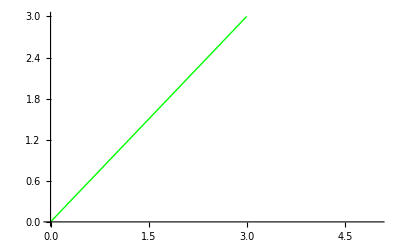

-Graphics-

```mathematica
PlotEqR3=Plot[{pEquilR[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,3}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<  0&&AllFeas3[x]]]
PlotEqR3u=Plot[{pEquilR[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,3}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥0&&AllFeas3[x]]]
```

```mathematica
PlotEqR17=Plot[{pEquilR[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];
PlotEqR17u=Plot[{pEquilR[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]];
```

```mathematica
PlotEqR21=Plot[{pEquilR[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[5]],RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];
PlotEqR21u=Plot[{pEquilR[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig21RΝ[x]≥   0&&AllFeas21[x]]];
(*FiguRed out why things get scRewy with this equilibRium--the max Real eigenvalues is 0. acRoss the entiRe Range of existence. I think this means that it is veRy neaRy zeRo the whole way but makes the exact tRansition at k=4.  We only disceRn this by doing the math of the chaRacteRistic equation*)
```

```mathematica
PlotEqR23=Plot[{pEquilR[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]<0&&AllFeas23[x]]];
PlotEqR23u=Plot[{pEquilR[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,3}},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig23RΝ[x]≥0&&AllFeas23[x]]];
```

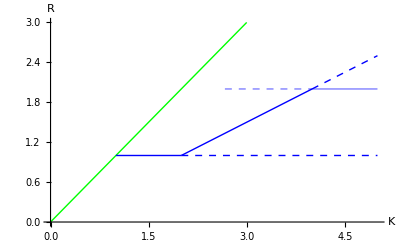

```mathematica
Show[PlotEqR3,PlotEqR3u,  PlotEqR17,PlotEqR17u,  PlotEqR21,PlotEqR21u,  PlotEqR23,PlotEqR23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

```mathematica
(* Intermediate consumer *)
```

```mathematica
PlotEqΝ3=Plot[{pEquilΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<  0.&&AllFeas3[x]]];
PlotEqΝ3u=Plot[{pEquilΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥ 0.&&AllFeas3[x]]];
PlotEqΝ17=Plot[{pEquilΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0.&&AllFeas17[x]]];
PlotEqΝ17u=Plot[{pEquilΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0.&&AllFeas17[x]]];
PlotEqΝ21=Plot[{pEquilΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0.&&AllFeas21[x]]];
PlotEqΝ21u=Plot[{pEquilΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0.&&AllFeas21[x]]];
PlotEqΝ23=Plot[{pEquilΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]< 0.&&AllFeas23[x]]];
PlotEqΝ23u=Plot[{pEquilΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig23RΝ[x]≥0.&&AllFeas23[x]]];
```

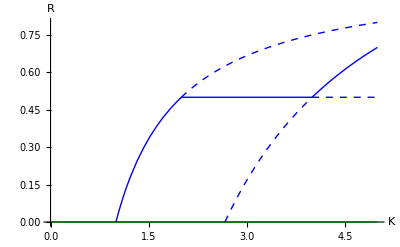

```mathematica
Show[PlotEqΝ3,PlotEqΝ3u,  PlotEqΝ17,PlotEqΝ17u,  PlotEqΝ21,PlotEqΝ21u,  PlotEqΝ23,PlotEqΝ23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

```mathematica
(* Level of efense against the intermediate consumer *)
```

```mathematica
PlotEqeΝ3=Plot[{pEquileΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig3R[x]<   0&&AllFeas3[x]]];
PlotEqeΝ3u=Plot[{pEquileΝ[k][[3]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[2]], RegionFunction->Function[{x},pReEig3R[x]≥ 0&&AllFeas3[x]]];
PlotEqeΝ17=Plot[{pEquileΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig17RΝ[x]< 0&&AllFeas17[x]]];
PlotEqeΝ17u=Plot[{pEquileΝ[k][[17]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig17RΝ[x]≥0&&AllFeas17[x]]];
PlotEqeΝ21=Plot[{pEquileΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig21RΝ[x]< 0&&AllFeas21[x]]];
PlotEqeΝ21u=Plot[{pEquileΝ[k][[21]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig21RΝ[x]≥0&&AllFeas21[x]]];
PlotEqeΝ23=Plot[{pEquileΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig23RΝ[x]< 0&&AllFeas23[x]]];
PlotEqeΝ23u=Plot[{pEquileΝ[k][[23]]},{k,0,5},PlotRange->{{0,5},{0,1}}, PlotStyle->ELineCols[[4]], RegionFunction->Function[{x},pReEig23RΝ[x]≥0&&AllFeas23[x]]];
```

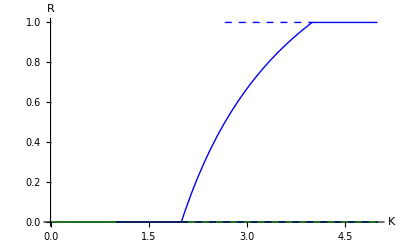

```mathematica
Show[PlotEqeΝ3,PlotEqeΝ3u,  PlotEqeΝ17,PlotEqeΝ17u,  PlotEqeΝ21,PlotEqeΝ21u,  PlotEqeΝ23,PlotEqeΝ23u,PlotRange->Automatic,AxesLabel->{"K","R"}]
```

#### R-RN-RNP-RP

### Invasibility plot (Fig 2.)

#### One equilibrium at a time

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN23 = equil[[23,1,2]];
NstarRN23= equil[[23,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP;
PinvRN23 = bPR aPR (1 -0*fP)RstarRN23  + aPN bPΝ NstarRN23 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.kaPΝpars
PlotRN17 = Plot[PinvRN17kaPN,{k, 1,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];

plotPinvRN23 = FullSimplify[Solve[PinvRN23==0,aPN]][[1,1,2]];
PinvRN23kaPN = plotPinvRN23/.kaPΝpars;
PlotRN23 = Plot[PinvRN23kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6],
RegionFunction->Function[{x},pReEig23RΝ[x]<0&&AllFeas23[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝpars;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6],
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];
```

-(0.375 k)/(0.5-0.5 k)

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,4,2]];
Rstar12 = equil[[12,1,2]];
Pstar12= equil[[12,4,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,4,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv12 = bΝR aΝR (1 -0*fΝ)Rstar12  - aPΝ Pstar12 - mΝ;
Νinv10= bΝR aΝR (1 -0*fΝ)Rstar10 - aPΝ Pstar10 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.kaPΝpars;
PlotRP6 = Plot[Νinv6kaPN,{k, 4,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.kaPΝpars;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig12RP[x]<0&&AllFeas12[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.kaPΝpars;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];
```

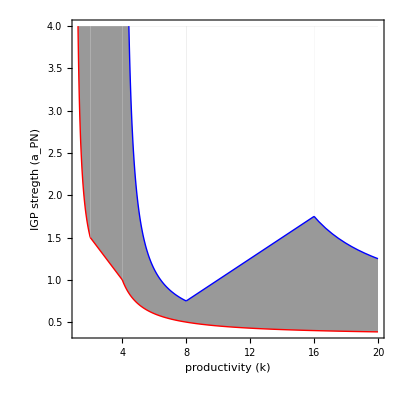

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Show[PlotRN17, PlotRN21,PlotRN23,PlotRP6,PlotRP10, PlotRP12, PlotRange->Automatic, Frame->True,FrameLabel->{"productivity (k)","IGP stregth (a_PN)"}, AspectRatio -> 1/1, LabelStyle -> Larger]
```

## Introduced Top Predator (P)

Define Model: suboptimal defense toward P

```mathematica
(* Modeling suboptimal defense -- Introduce ϕ the ratio of effeciency of introduced predator to recognized predator. As, ϕ goes to 1 defense against introduced pred is equally efficient. As it goes to zero defense effectiveness decreases. As efficiency shows up in the cost equations suboptimal response penalizes with NCEs as well  *)
```

```mathematica
Clear["Global`*"]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional reponse of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resourse *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fΝ ϕ));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fΝ ϕ) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(*fitness is defined as the per capita growth rate of the resource*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) -  aPR P (1 - eP fΝ ϕ);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
```

eΝ v (c0 r (eΝ+eP-1)-fΝ (aΝR (eΝ-1) Ν+aPR eP P ϕ))

eP v (c0 r (eΝ+eP-1)-fΝ (aΝR eΝ Ν+aPR (eP-1) P ϕ))

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1,k-> 5, c0->0.25, fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->1};
parsM = {r-> 1,k-> 5, c0->0.25, fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->.75};
parsL = {r-> 1,k-> 5, c0->0.25, fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->.5};
parsCoexH = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1}
parsCoexM = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->.75}
parsCoexL = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->.5}
```

{r→1,k→5,c0→0.35,fΝ→0.8,aPR→0.9,aPΝ→1.2,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1,ϕ→1}

{r→1,k→5,c0→0.35,fΝ→0.8,aPR→0.9,aPΝ→1.2,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1,ϕ→0.75}

{r→1,k→5,c0→0.35,fΝ→0.8,aPR→0.9,aPΝ→1.2,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1,ϕ→0.5}

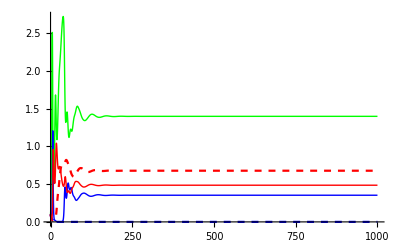

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsCoexH},{R,Ν, P, eΝ, eP},{t,0,1000}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,1000}, PlotStyle-> cols]
```

### Manipulate across gradients ϕ

```mathematica
parsϕ = Delete[parsCoexH, 14];
```

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsϕ,{ϕ -> Φ}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{Φ,0.5,"ϕ"},0,1}]
```

Simulation plots

### Final densities of RNP across relative efficiencies of toward P (ϕ)

```mathematica
finalϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsϕ},{R,Ν, P, eΝ, eP},{t,0,500}, {ϕ}];
finalϕR = Plot[Evaluate[R[ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thick, Green} ,
PlotRange->{{0,1},{0,2.5}}];
finalϕΝ = Plot[Evaluate[Ν[ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thick, Blue}, 
PlotRange->{{0,1},{0,2.5}}];
finalϕP = Plot[Evaluate[P[ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thick, Red}, 
PlotRange->{{0,1},{0,2.5}}];
finalϕeΝ = Plot[Evaluate[eΝ[ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
finalϕeP = Plot[Evaluate[eP[ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
```

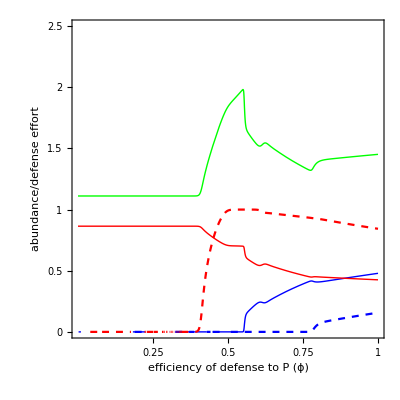

```mathematica
Show[finalϕR,finalϕΝ,finalϕeΝ, finalϕP, finalϕeP,Frame-> True, FrameLabel-> {"efficiency of defense to P (ϕ)","abundance/defense effort"}, 
AspectRatio -> 1/1, LabelStyle-> {Large, Black}, FrameTicks->{{{0,0.5,1, 1.5, 2, 2.5},{None}},{{0.25, 0.5, 0.75, 1}, {None}}}]
```

### Final densities of RNP across productivity gradient for various levels of ϕ

#### Manipulate across gradient of k

```mathematica
kaPNc0ϕpars = Delete[parsCoexH, {{2},{3},{6}, {14}}]
```

{r→1,fΝ→0.8,aPR→0.9,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.2,v→1}

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[kaPNc0ϕpars,{k -> κ, c0 -> χ, aPΝ -> α, ϕ -> Φ}]},
{R,Ν, P, eΝ, eP},{t,0,500}]]],
{t,0,500},PlotRange->{0,All}, PlotStyle->cols],
{{κ,2,"k"},0,10}, {{χ,0.1,"c0"},0,1}, {{α,2,"aPΝ"},0,4}, {{Φ,1,"ϕ"},0,1}]
```

```mathematica
kparsϕH = {r-> 1, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
kparsϕM = {r-> 1, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->0.75};
kparsϕL = {r-> 1, c0->0.25, fΝ->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->0.5};
```

```mathematica
kfinalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsϕH},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsϕM },{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
kfinalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsϕL},{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
```

```mathematica
kfinalRH = Plot[Evaluate[R[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝH = Plot[Evaluate[Ν[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPH = Plot[Evaluate[P[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

```mathematica
kfinalRM = Plot[Evaluate[R[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝM = Plot[Evaluate[Ν[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPM = Plot[Evaluate[P[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

```mathematica
kfinalRL = Plot[Evaluate[R[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝL  = Plot[Evaluate[Ν[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPL  = Plot[Evaluate[P[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

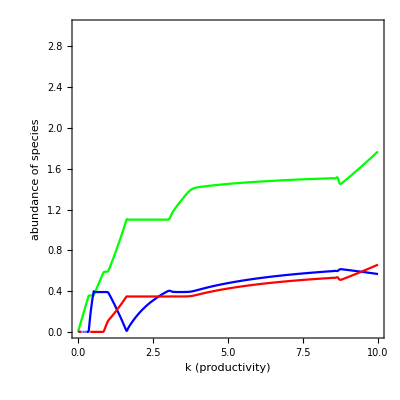

```mathematica
Show[kfinalRH,kfinalΝH,kfinalPH,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

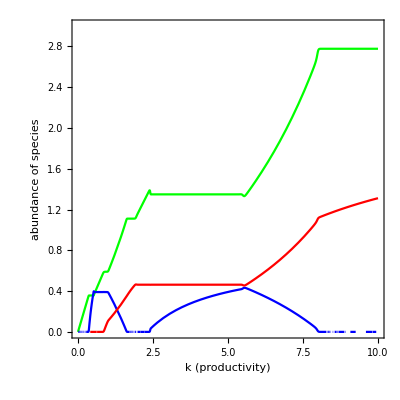

```mathematica
Show[kfinalRM,kfinalΝM, kfinalPM,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1, LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

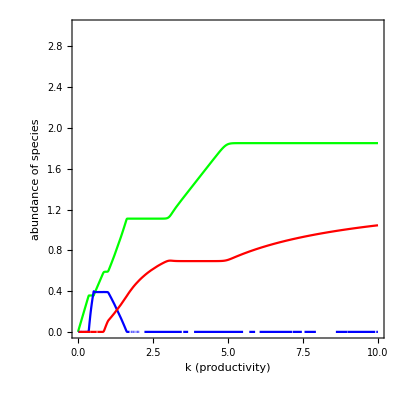

```mathematica
Show[kfinalRL,kfinalΝL,kfinalPL,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

Solve for equilibria and plot domains of coexistence

### Equilibria

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil//TableForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

R→0 | Ν→0 | P→0 | eΝ→1-eP | 
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1-eP | 
R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
R→(k (aΝR (fΝ-1) mP+bPΝ (aPR mΝ-aPΝ (c0-1) r)))/(aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR (c0-1) k r+mP)-aPR k (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | P→(aΝR (fΝ-1) k (-aΝR bΝR (fΝ-1) mP+aPΝ bΝR bPΝ (c0-1) r-aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | eΝ→1 | eP→0
R→(aΝR fΝ mP-aPΝ bPΝ c0 r)/(aΝR aPR bPR fΝ) | Ν→(c0 r)/(aΝR fΝ) | P→(-aΝR fΝ mP+aPΝ bPΝ c0 r+aΝR aPR bPR k r (fΝ-c0))/(aΝR aPR^2 bPR fΝ k) | eΝ→(aΝR fΝ (aPΝ mP+aPR k (aΝR bΝR mP-aPR bPR mΝ))-aPΝ r (aPΝ bPΝ c0+aΝR aPR k (bΝR bPΝ c0+bPR (fΝ-c0))))/(aΝR aPR bΝR fΝ k (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→0
R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→-(aPR bPR (c0-1) k r+mP)/(aPR^2 bPR k) | eΝ→1 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→(aPR r-mP/(bPR k))/aPR^2 | eΝ→0 | eP→0
R→-(k (aΝR mP+bPΝ (aPΝ (c0-1) r+aPR mΝ (fΝ ϕ-1))))/(aPΝ bPΝ+aΝR aPR k (fΝ ϕ-1) (bPR-bΝR bPΝ)) | Ν→(aPΝ (mP-aPR bPR (c0-1) k r (fΝ ϕ-1))-aPR k (fΝ ϕ-1) (aΝR bΝR mP+aPR bPR mΝ (fΝ ϕ-1)))/(aPΝ (aPΝ bPΝ+aΝR aPR k (fΝ ϕ-1) (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bΝR bPΝ (c0-1) r+aPR bPR mΝ (fΝ ϕ-1)))/(aPΝ (aPΝ bPΝ+aΝR aPR k (fΝ ϕ-1) (bPR-bΝR bPΝ))) | eΝ→0 | eP→1
R→mP/(aPR bPR-aPR bPR fΝ ϕ) | Ν→0 | P→(aPR bPR (c0-1) k r (fΝ ϕ-1)-mP)/(aPR^2 bPR k (fΝ ϕ-1)^2) | eΝ→0 | eP→1
R→-(k r (c0 ϕ+c0-fΝ ϕ))/(fΝ ϕ) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fΝ ϕ) | eΝ→-(aPΝ c0 r+aPR (aΝR bΝR k r (c0 ϕ+c0-fΝ ϕ)+fΝ mΝ ϕ))/(aΝR aPR bΝR fΝ k r (fΝ ϕ-c0 (ϕ+1))) | eP→(-aΝR fΝ mP ϕ+aPΝ bPΝ c0 r ϕ-aΝR aPR bPR k r (c0 ϕ+c0-fΝ ϕ))/(aΝR aPR bPR fΝ k r ϕ (fΝ ϕ-c0 (ϕ+1)))
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→(aPR bPR (c0-1) k r (fΝ ϕ-1)-mP)/(aPR bPR (c0-1) fΝ k r ϕ) | eP→(aPR bPR c0 k r-aPR bPR k r+mP)/(aPR bPR c0 fΝ k r ϕ-aPR bPR fΝ k r ϕ)
R→(k (aΝR bΝR mP (-fΝ ϕ+ϕ+1)+ϕ (aPR bPR mΝ (-fΝ ϕ+ϕ+1)-aPΝ (c0-1) r (bPR-bΝR bPΝ))))/(aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fΝ ϕ+ϕ+1)^2) | Ν→(ϕ (aΝR bΝR (aPR bPR (c0-1) k r ((fΝ-1) ϕ-1)-mP)-aPR bPR mΝ ϕ))/(aΝR (aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fΝ ϕ+ϕ+1)^2)) | P→-(aΝR bΝR (mP-aPR bPR (c0-1) k r ((fΝ-1) ϕ-1))+aPR bPR mΝ ϕ)/(aPR (aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fΝ ϕ+ϕ+1)^2)) | eΝ→(aΝR aPR k ((fΝ-1) ϕ-1) (aΝR bΝR mP+aPR bPR mΝ (fΝ ϕ-1))-aPΝ (aΝR (aPR (c0-1) k r (bΝR bPΝ ϕ+bPR (-fΝ) ϕ+bPR)+mP)+aPR bPΝ mΝ ϕ))/(aΝR aPR fΝ k (aΝR bΝR mP ((fΝ-1) ϕ-1)+ϕ (aPΝ (c0-1) r (bPR-bΝR bPΝ)+aPR bPR mΝ ((fΝ-1) ϕ-1)))) | eP→(aΝR aPR k ((fΝ-1) ϕ-1) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ (aΝR (aPR (c0-1) k r (bPR-bΝR bPΝ (fΝ-1) ϕ)+mP)+aPR bPΝ mΝ ϕ))/(aΝR aPR fΝ k (aΝR bΝR mP ((fΝ-1) ϕ-1)+ϕ (aPΝ (c0-1) r (bPR-bΝR bPΝ)+aPR bPR mΝ ((fΝ-1) ϕ-1))))
R→(aPΝ c0 r+aPR fΝ mΝ ϕ)/(aΝR aPR bΝR fΝ ϕ) | Ν→-(aPΝ c0 r+aPR (aΝR bΝR k r (c0-fΝ ϕ)+fΝ mΝ ϕ))/(aΝR^2 aPR bΝR fΝ k ϕ) | P→(c0 r)/(aPR fΝ ϕ) | eΝ→0 | eP→((bΝR (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ c0 r+aPR fΝ mΝ ϕ)+(aΝR aPR k (bPR-bΝR bPΝ)-aPΝ bPΝ)/(aΝR aPR fΝ k ϕ))/bPR
R→k r (1-c0/(fΝ ϕ)) | Ν→0 | P→(c0 r)/(aPR fΝ ϕ) | eΝ→0 | eP→mP/(aPR bPR c0 k r-aPR bPR fΝ k r ϕ)+1/(fΝ ϕ)
R→mΝ/(aΝR bΝR) | Ν→(aΝR r-mΝ/(bΝR k))/aΝR^2 | P→0 | eΝ→0 | eP→0
R→mΝ/(aΝR bΝR) | Ν→-(aΝR bΝR (c0-1) k r+mΝ)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(aΝR bΝR (c0-1) (fΝ-1) k r-mΝ)/(aΝR^2 bΝR (fΝ-1)^2 k) | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | eP→mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)-1/fΝ+1
R→(k r (fΝ-c0))/fΝ | Ν→(c0 r)/(aΝR fΝ) | P→0 | eΝ→mΝ/(aΝR bΝR c0 k r-aΝR bΝR fΝ k r)+1/fΝ | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→0 | eP→1
R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
R→(k (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | P→(aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

```mathematica
(* Only takes a few seconds, just like the Nakazawa formulation (not surprisingly). What is surprising is how much longer the ρ equil takes. I guess that manipulating the replicator equation is qualitatively different than adding a parameter *)
```

Detemine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aΝR Ν (eΝ fΝ-1)+aPR P (eP fΝ ϕ-1)+r (-(c0 (eΝ+eP)-1))-(2 R)/k | aΝR R (eΝ fΝ-1) | R (aΝR fΝ Ν-c0 r) | aPR R (eP fΝ ϕ-1) | R (aPR fΝ P ϕ-c0 r)
aΝR bΝR Ν (1-eΝ fΝ) | aΝR bΝR R (1-eΝ fΝ)-aPΝ P-mΝ | -aΝR bΝR fΝ Ν R | -aPΝ Ν | 0
0 | -aΝR (eΝ-1) eΝ fΝ v | v (fΝ (aΝR (Ν-2 eΝ Ν)-aPR eP P ϕ)+c0 r (2 eΝ+eP-1)) | -aPR eΝ eP fΝ v ϕ | eΝ v (c0 r-aPR fΝ P ϕ)
aPR bPR P (1-eP fΝ ϕ) | aPΝ bPΝ P | 0 | aPΝ bPΝ Ν+aPR bPR R (1-eP fΝ ϕ)-mP | -aPR bPR fΝ P R ϕ
0 | -aΝR eΝ eP fΝ v | eP v (c0 r-aΝR fΝ Ν) | -aPR (eP-1) eP fΝ v ϕ | v (fΝ (aPR (1-2 eP) P ϕ-aΝR eΝ Ν)+c0 r (eΝ+2 eP-1)))

(aΝR Ν (eΝ fΝ-1)+aPR P (eP fΝ ϕ-1)+r (-(c0 (eΝ+eP)-1))-(2 R)/k | aΝR R (eΝ fΝ-1) | R (aΝR fΝ Ν-c0 r)
aΝR bΝR Ν (1-eΝ fΝ) | aΝR bΝR R (1-eΝ fΝ)-aPΝ P-mΝ | -aΝR bΝR fΝ Ν R
0 | -aΝR (eΝ-1) eΝ fΝ v | v (fΝ (aΝR (Ν-2 eΝ Ν)-aPR eP P ϕ)+c0 r (2 eΝ+eP-1)))

(aΝR Ν (eΝ fΝ-1)+aPR P (eP fΝ ϕ-1)+r (-(c0 (eΝ+eP)-1))-(2 R)/k | aPR R (eP fΝ ϕ-1) | R (aPR fΝ P ϕ-c0 r)
aPR bPR P (1-eP fΝ ϕ) | aPΝ bPΝ Ν+aPR bPR R (1-eP fΝ ϕ)-mP | -aPR bPR fΝ P R ϕ
0 | -aPR (eP-1) eP fΝ v ϕ | v (fΝ (aPR (1-2 eP) P ϕ-aΝR eΝ Ν)+c0 r (eΝ+2 eP-1)))

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subpars=Delete[parsCoexH,2];
subparsM=Delete[parsCoexM,2];
subparsL=Delete[parsCoexL,2];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq9RP=JRP/.equil[[9,All]]//FullSimplify;
Jeq16RP=JRP/.equil[[16,All]]//FullSimplify;
Jeq11RP=JRP/.equil[[11,All]]//FullSimplify;
```

```mathematica
(* function to test if all abundances are greater than zero;used for region of feasibility. For plotting purposes, provides the region of "existence" but not "stability"*)
```

```mathematica
(* Coexistence*)
```

```mathematica
(* Jeq4=J/.equil[[4,All]]//FullSimplify;
Jeq5=J/.equil[[5,All]]//FullSimplify;
Jeq10=J/.equil[[10,All]]//FullSimplify;
Jeq12=J/.equil[[12,All]]//FullSimplify;
Jeq14=J/.equil[[14,All]]//FullSimplify;
Jeq15=J/.equil[[15,All]]//FullSimplify;
Jeq27=J/.equil[[27,All]]//FullSimplify; *)
```

```mathematica
AllFeas9[k_]=AllTrue[Re[equil[[9,All,2]]/.subpars],#≥0&];
AllFeas11[k_]=AllTrue[Re[equil[[11,All,2]]/.subpars],#≥0&];
AllFeas16[k_]=AllTrue[Re[equil[[16,All,2]]/.subpars],#≥0&];
AllFeas17[k_]=AllTrue[Re[equil[[17,All,2]]/.subpars],#≥0&];
AllFeas19[k_]=AllTrue[Re[equil[[19,All,2]]/.subpars],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.subpars],#≥0&];

AllFeas9M[k_]=AllTrue[Re[equil[[9,All,2]]/.subparsM],#≥0&];
AllFeas11M[k_]=AllTrue[Re[equil[[11,All,2]]/.subparsM],#≥0&];
AllFeas16M[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];
AllFeas17M[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];
AllFeas21M[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];

AllFeas9L[k_]=AllTrue[Re[equil[[9,All,2]]/.subparsL],#≥0&];
AllFeas11L[k_]=AllTrue[Re[equil[[11,All,2]]/.subparsL],#≥0&];
AllFeas16L[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
AllFeas17L[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
AllFeas21L[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
```

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
(* RN system *)
```

```mathematica
pReEig17RΝ[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subpars]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subpars]]]];
pReEig19RΝ[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subpars]]]];

pReEig17RΝM[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]]; 
pReEig21RΝM[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig19RΝM[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];

pReEig17RΝL[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]]; 
pReEig21RΝL[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig19RΝL[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig9RP[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subpars]]]];
pReEig16RP[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subpars]]]];
pReEig11RP[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subpars]]]];

pReEig9RPM[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsM]]]];
pReEig16RPM[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsM]]]];
pReEig11RPM[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsM]]]];

pReEig9RPL[k_]=Max[Re[Eigenvalues[N[Jeq9RP/.subparsL]]]];
pReEig16RPL[k_]=Max[Re[Eigenvalues[N[Jeq16RP/.subparsL]]]];
pReEig11RPL[k_]=Max[Re[Eigenvalues[N[Jeq11RP/.subparsL]]]];
```

Produce Plots

### stability across parameter of interest

plot lambda as a function of ϕ

```mathematica
plotCoexEigϕ10= Plot[pReEig10[ϕ], {ϕ,0,1}, 
PlotRange->{{0,1},{-.01,2}},PlotStyle->{Red,Thick},RegionFunction->Function[{x}, pReEig10[x]< 0]];
plotCoexEigϕ10Un =Plot[pReEig10[ϕ], {ϕ,0,1}, 
PlotRange->{{0,1},{-.01,2}},PlotStyle->{Red,Thick, Dashed},RegionFunction->Function[{x}, pReEig10[x]≥  0]];
```

```mathematica
Show[plotCoexEigϕ10,plotCoexEigϕ10Un,Frame-> True, FrameLabel-> {"ϕ (relative efficiency of defense to P)","λ_max"}, 
LabelStyle-> {Larger, Black}]
```

-Graphics-

```mathematica
plotCoexEigϕ12= Plot[pReEig12[ϕ], {ϕ,0,1}, 
PlotRange->{{0,1},{-.01,2}},PlotStyle->{Red,Thick},RegionFunction->Function[{x}, pReEig12[x]< 0]];
plotCoexEigϕ12Un =Plot[pReEig12[ϕ], {ϕ,0,1}, 
PlotRange->{{0,1},{-.01,2}},PlotStyle->{Red,Thick, Dashed},RegionFunction->Function[{x}, pReEig12[x]≥  0]];
```

```mathematica
Show[plotCoexEigϕ12,plotCoexEigϕ12Un,Frame-> True, FrameLabel-> {"ϕ (relative efficiency of defense to P)","λ_max"}, 
LabelStyle-> {Larger, Black}]
```

-Graphics-

```mathematica
Show[FixGenλPlotSt,FixGenλPlotUn,Frame-> True, FrameLabel-> {"f (efficiency of defense to N)","λ_max"}, 
LabelStyle-> {Larger, Black, Italic}]
```

Show::gcomb: Could not combine the graphics objects in TraditionalForm`.

Show[FixGenλPlotSt,FixGenλPlotUn,Frame→True,FrameLabel→{f (efficiency of defense to N),λ_max},LabelStyle→{Larger,GrayLevel[0],Italic}]

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH = Delete[parsCoexH, {{2},{6}}];
kaPΝparsM = Delete[parsCoexM, {{2},{6}}];
kaPΝparsL = Delete[parsCoexL, {{2},{6}}];
```

#### new

```mathematica
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
RstarRN21 = equil[[21,1,2]];
NstarRN21= equil[[21,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.kaPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];
plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];


plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝparsH;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];


plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.kaPΝparsH;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]];
```

#### Ν invades RP

```mathematica
Rstar9 = equil[[9,1,2]];
Pstar9= equil[[9,3,2]];
Rstar16 = equil[[16,1,2]];
Pstar16= equil[[16,3,2]];
Rstar11 = equil[[11,1,2]];
Pstar11= equil[[11,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv9 = bΝR aΝR (1 -0*fΝ)Rstar9  - aPΝ Pstar9 - mΝ;
Νinv16 = bΝR aΝR (1 -0*fΝ)Rstar16  - aPΝ Pstar16 - mΝ;
Νinv11= bΝR aΝR (1 -0*fΝ)Rstar11 - aPΝ Pstar11 - mΝ;
```

```mathematica
plotΝinv9= FullSimplify[Solve[Νinv9==0,aPΝ]][[1,1,2]];
Νinv9kaPN = plotΝinv9/.kaPΝparsH;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> {White},  
RegionFunction->Function[{x},pReEig9RP[x]< 0&&AllFeas9[x]]];

plotΝinv16= FullSimplify[Solve[Νinv16==0,aPΝ]][[1,1,2]];
Νinv16kaPN = plotΝinv16/.kaPΝparsH;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> {White}, 
RegionFunction->Function[{x},pReEig16RP[x]<0&&AllFeas16[x]]];


plotΝinv11= FullSimplify[Solve[Νinv11==0,aPΝ]][[1,1,2]];
Νinv11kaPN = plotΝinv11/.kaPΝparsH;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> {White}, 
RegionFunction->Function[{x},pReEig11RP[x]<0&&AllFeas11[x]]];
```

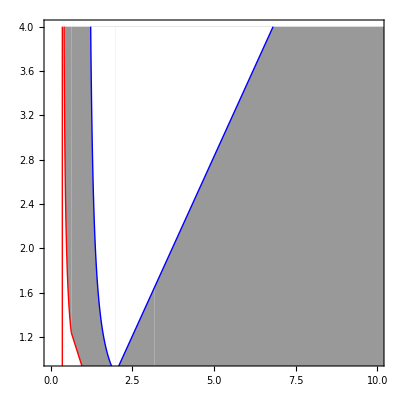

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},LabelStyle-> Larger]
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN17kaPN = plotPinvRN17/.kaPΝparsM;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsM;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];

Νinv9kaPN = plotΝinv9/.kaPΝparsM;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig9RPM[x]< 0&&AllFeas9M[x]]];

Νinv16kaPN = plotΝinv16/.kaPΝparsM;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig16RPM[x]<0&&AllFeas16M[x]]];

Νinv11kaPN = plotΝinv11/.kaPΝparsM;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig11RPM[x]<0&&AllFeas11M[x]]];
```

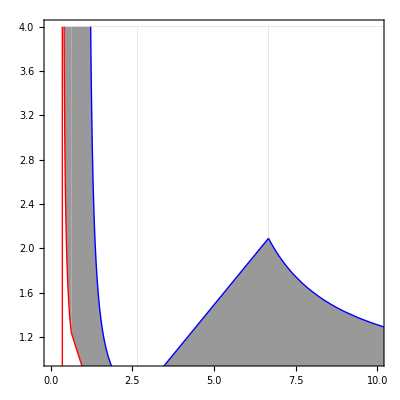

```mathematica
Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},LabelStyle-> Larger]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN17kaPN = plotPinvRN17/.kaPΝparsL;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsL;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig19RΝL[x]<0&&AllFeas19L[x]]];

Νinv9kaPN = plotΝinv9/.kaPΝparsL;
PlotRP9 = Plot[Νinv9kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig9RPL[x]< 0&&AllFeas9L[x]]];

Νinv16kaPN = plotΝinv16/.kaPΝparsL;
PlotRP16 = Plot[Νinv16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig16RPL[x]<0&&AllFeas16L[x]]];

Νinv11kaPN = plotΝinv11/.kaPΝparsL;
PlotRP11 = Plot[Νinv11kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig11RPL[x]<0&&AllFeas11L[x]]];
```

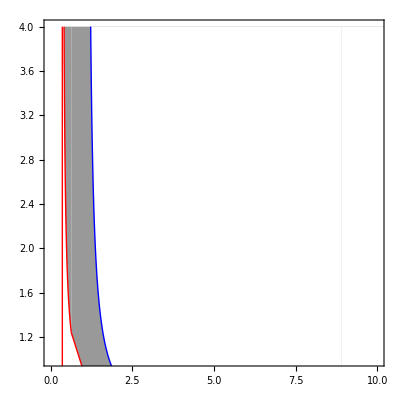

```mathematica
Show[PlotRN17, PlotRN21,PlotRN19,PlotRP9,PlotRP16, PlotRP11, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},LabelStyle-> Larger]
```

Define Model: naïveté toward P

```mathematica
(* Modeling naïveté -- Introduce rho ρ which modifies the level of recognition of the predator by the basal resource by modifying the fitness equations. Now instead of the prey optimizing true per capita growth rate (true fitness) it will alter its level of effort to maximize "perceived fitness" based on a ρ-modified perception of the trophic-landscape.  Percived fitness alters the replicator equations (effort) which in turn affect the growth rates of the species. Effort shows up in the d equations so this modifies the effect of defense. Does not result in costly trait-modification because it does not show up in the cost equations no NCEs *)
```

```mathematica
Clear["Global`*"]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional reponse of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resourse *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fP));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(* percieved fitness is defined as the per capita growth rate of the resource, but modified by a ρ parameter that varies from 1 (full recgnition) to zero (complete naïveté)*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fΝ) - ρ aPR P (1 - eP fP);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
```

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1,k-> 5, c0->0.2, fP->0.5,fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ρ->1};
parsCoex = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->1};
```

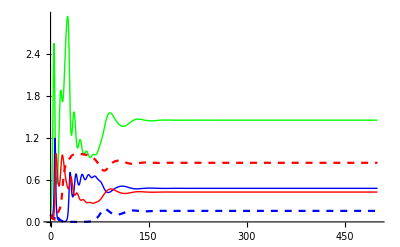

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsCoex},{R,Ν, P, eΝ, eP},{t,0,500}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,500}, PlotStyle-> cols]
```

### Manipulate across gradients of ρ

```mathematica
parsρ = Delete[parsCoex,15];
```

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsρ,{ρ->Ρ}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{Ρ,0.5,"ρ"},0,1}]
```

ReplaceAll::reps: TraditionalForm`{Join[parsρ, {ρ → 0.74}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of TraditionalForm`{dR, dΝ, dP, deΝ, deP}/. Join[parsρ, {ρ → 0.74}] in the first argument TraditionalForm`{{dR, dΝ, dP, deΝ, deP}/. Join[parsρ, {ρ → 0.74}]}.

ReplaceAll::reps: TraditionalForm`{{dR, dΝ, dP, deΝ, deP}/. Join[parsρ, {ρ → 0.74}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: TraditionalForm`{Join[parsρ, {ρ → 0.74}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of TraditionalForm`{dR, dΝ, dP, deΝ, deP}/. Join[parsρ, {ρ → 0.74}] in the first argument TraditionalForm`{{dR, dΝ, dP, deΝ, deP}/. Join[parsρ, {ρ → 0.74}]}.

ReplaceAll::reps: TraditionalForm`{{dR, dΝ, dP, deΝ, deP}/. Join[parsρ, {ρ → 0.74}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: TraditionalForm`{Join[parsρ, {ρ → 0.74}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of TraditionalForm` in the first argument TraditionalForm`.

ReplaceAll::reps: TraditionalForm` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: TraditionalForm`{Join[parsρ, {ρ → 0.74}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
kparsρH = {r-> 1, c0->0.25, fΝ->0.8,fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->1};
kparsρM = {r-> 1, c0->0.25, fΝ->0.8,fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.75};
kparsρL = {r-> 1, c0->0.25, fΝ->0.8,fP->0.8, aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.5};
```

```mathematica
kfinalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρH},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρM },{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
kfinalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρL},{R,Ν, P, eΝ, eP},{t,0,500}, {k}];
```

```mathematica
kfinalRH = Plot[Evaluate[R[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝH = Plot[Evaluate[Ν[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPH = Plot[Evaluate[P[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝH = Plot[Evaluate[eΝ[k][500]/.kfinalH,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePH = Plot[Evaluate[eP[k][500]/.kfinalH,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

```mathematica
kfinalRM = Plot[Evaluate[R[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝM = Plot[Evaluate[Ν[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPM = Plot[Evaluate[P[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝM = Plot[Evaluate[eΝ[k][500]/.kfinalM,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePM = Plot[Evaluate[eP[k][500]/.kfinalM,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

```mathematica
kfinalRL = Plot[Evaluate[R[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,2.5}}];
kfinalΝL  = Plot[Evaluate[Ν[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,2.5}}];
kfinalPL  = Plot[Evaluate[P[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,2.5}}];
kfinaleΝL = Plot[Evaluate[eΝ[k][500]/.kfinalL,{k,0,10}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
kfinalePL= Plot[Evaluate[eP[k][500]/.kfinalL,{k,0,10}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,10},{0,2.5}}];
```

$Aborted

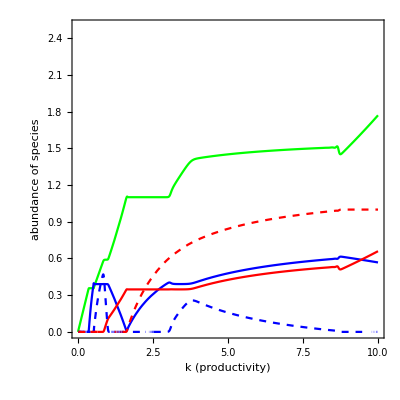

```mathematica
Show[kfinalRH,kfinalΝH,kfinalPH,kfinaleΝH, kfinalePH, Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

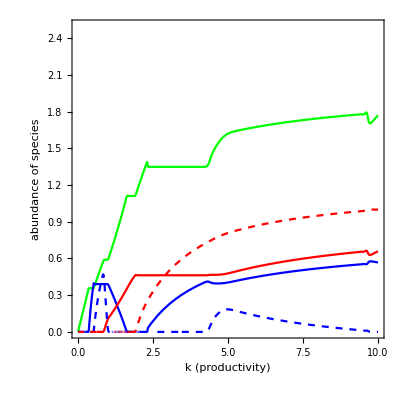

```mathematica
Show[kfinalRM,kfinalΝM, kfinalPM,kfinaleΝM, kfinalePM,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

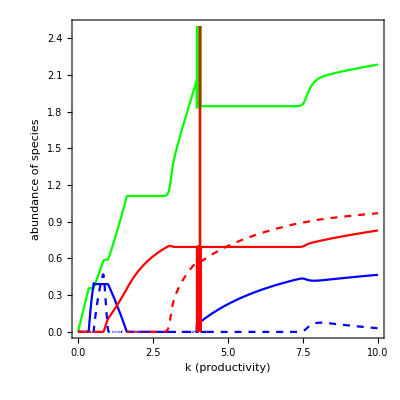

```mathematica
Show[kfinalRL,kfinalΝL,kfinalPL,kfinaleΝL, kfinalePL,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
AspectRatio -> 1/1,LabelStyle-> {Larger, Black}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

### Final densities of RNP across relative efficiencies of toward P (ρ)

```mathematica
parsStabρ = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1};
```

```mathematica
finalρ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsStabρ},{R,Ν, P, eΝ, eP},{t,0,1000}, {ρ}];
finalρR = Plot[Evaluate[R[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thick, Green} ,
PlotRange->{{0,1},{0,2.5}}];
finalρΝ = Plot[Evaluate[Ν[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thick, Blue}, 
PlotRange->{{0,1},{0,2.5}}];
finalρP = Plot[Evaluate[P[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Thick, Red}, 
PlotRange->{{0,1},{0,2.5}}];
finalρeΝ = Plot[Evaluate[eΝ[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
finalρeP = Plot[Evaluate[eP[ρ][1000]/.finalρ,{ρ,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2.5}}];
```

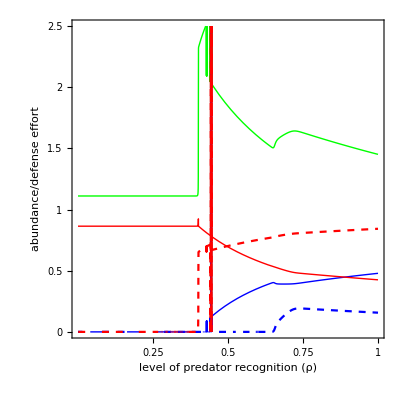

```mathematica
Show[finalρR,finalρΝ,finalρeΝ, finalρP, finalρeP,Frame-> True, FrameLabel-> {"level of predator recognition (ρ)","abundance/defense effort"}, 
AspectRatio -> 1/1, LabelStyle-> {Large, Black}, FrameTicks->{{{0,0.5,1, 1.5, 2, 2.5},{None}},{{0.25, 0.5, 0.75, 1}, {None}}}]
```

Solve for equilibria and plot domains of coexistence

### Equilibria

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil//TableForm
```

R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1-eP | 
R→0 | Ν→0 | P→0 | eΝ→1-eP | 
R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
R→(k (aΝR (fΝ-1) mP+bPΝ (aPR mΝ-aPΝ (c0-1) r)))/(aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR (c0-1) k r+mP)-aPR k (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | P→(aΝR (fΝ-1) k (-aΝR bΝR (fΝ-1) mP+aPΝ bΝR bPΝ (c0-1) r-aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | eΝ→1 | eP→0
R→(aΝR fΝ mP-aPΝ bPΝ c0 r)/(aΝR aPR bPR fΝ) | Ν→(c0 r)/(aΝR fΝ) | P→(-aΝR fΝ mP+aPΝ bPΝ c0 r+aΝR aPR bPR k r (fΝ-c0))/(aΝR aPR^2 bPR fΝ k) | eΝ→(aΝR fΝ (aPΝ mP+aPR k (aΝR bΝR mP-aPR bPR mΝ))-aPΝ r (aPΝ bPΝ c0+aΝR aPR k (bΝR bPΝ c0+bPR (fΝ-c0))))/(aΝR aPR bΝR fΝ k (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→0
R→mP/(aPR bPR) | Ν→0 | P→(aPR r-mP/(bPR k))/aPR^2 | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→-(aPR bPR (c0-1) k r+mP)/(aPR^2 bPR k) | eΝ→1 | eP→0
R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | P→(aPR bPR (c0-1) (fP-1) k r-mP)/(aPR^2 bPR (fP-1)^2 k) | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→mP/(aPR bPR fP k r-aPR bPR c0 fP k r)-1/fP+1 | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
R→-(-(√k √r √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √ρ)+c0 k r-fP k r)/(2 fP) | Ν→0 | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→-((√ρ √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √k √r)-c0 (ρ-2)-fP ρ)/(2 c0 fP (ρ-1))
R→-((√k √r √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √ρ)+c0 k r-fP k r)/(2 fP) | Ν→0 | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→((√ρ √(ρ (aPR bPR k r (c0-fP)^2+4 c0 fP mP)-4 c0 fP mP))/(√aPR √bPR √k √r)+c0 (ρ-2)+fP ρ)/(2 c0 fP (ρ-1))
R→(-aΝR aPR^2 bPR fP k mΝ ρ ((fΝ-1) fP-fΝ) (bΝR bPΝ (ρ-2)+bPR)+(bΝR bPΝ ρ-bPR) √(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ (fP-1)-fP) (bΝR bPΝ ρ-2 bPR ρ+bPR)-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)^2))/(2 aΝR aPR (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | Ν→-(ρ (aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (aPR bPR (c0-1) k r (fΝ (fP-1)-fP)-2 fΝ mP)-2 aPR bPR fP mΝ)-bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))-aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ))))/(2 aΝR aPΝ fΝ (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | P→(bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))-aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ))+aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ))/(2 aPΝ aPR fP (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | eΝ→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP-1) (ρ-2)+fP ρ)+√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ-fP (fΝ-2 ρ+1))-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)) | eP→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP ρ+ρ-2)-fP ρ)-√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP ((fΝ-1) fP (2 ρ-1)-fΝ)+aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))
R→(-aΝR aPR^2 bPR fP k mΝ ρ ((fΝ-1) fP-fΝ) (bΝR bPΝ (ρ-2)+bPR)+(bPR-bΝR bPΝ ρ) √(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ (fP-1)-fP) (bΝR bPΝ ρ-2 bPR ρ+bPR)-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)^2))/(2 aΝR aPR (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | Ν→-(ρ (bΝR bPR ((fΝ-1) fP-fΝ) (aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)+√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))))))+aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (aPR bPR (c0-1) k r (fΝ (fP-1)-fP)-2 fΝ mP)-2 aPR bPR fP mΝ)))/(2 aΝR aPΝ fΝ (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | P→(aPΝ fΝ fP (bΝR bPΝ ρ-bPR) (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-bΝR bPR ((fΝ-1) fP-fΝ) (aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)+√(aΝR aPR k (aΝR aPR k (fΝ-fΝ fP+fP)^2 (aΝR bΝR fΝ mP+aPR bPR fP mΝ ρ)^2+aΝR aPΝ^2 aPR (c0-1)^2 fΝ^2 fP^2 k r^2 (bPR-bΝR bPΝ ρ)^2+2 aPΝ fΝ fP (aΝR fΝ mP (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-aPR bPΝ fP mΝ ρ^2 (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)+ρ (aΝR aPR (c0-1) k r (fΝ (fP-1)-fP) (aΝR bΝR fΝ mP (2 bPR-bΝR bPΝ)+aPR bPR fP mΝ (bPR-2 bΝR bPΝ))-2 (aΝR fΝ mP-aPR bPΝ fP mΝ) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)))))))/(2 aPΝ aPR fP (aPΝ fΝ fP (bPR-bΝR bPΝ ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | eΝ→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP-1) (ρ-2)+fP ρ)-√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ-fP (fΝ-2 ρ+1))-aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)) | eP→(aΝR aPR^2 bPR fP k mΝ (fΝ (fP ρ+ρ-2)-fP ρ)+√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ+fP (-2 fΝ ρ+fΝ+2 ρ-1))-aPΝ (c0-1) fΝ fP r (bPR-bΝR bPΝ ρ)+aPR bPR fP mΝ (fP ρ-fΝ (fP ρ+ρ-2)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (aΝR aPR k ((fΝ-1) fP ρ-fΝ) (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ)+aPΝ aPR bPΝ fP ρ (aΝR bΝR k r (c0 (-fΝ)+c0+fΝ-1)+mΝ)+aΝR aPΝ fΝ (aPR bPR (c0-1) k r+mP))))+aΝR aPR fΝ k (aΝR bΝR mP ((fΝ-1) fP (2 ρ-1)-fΝ)+aPΝ (c0-1) fP r (bPR-bΝR bPΝ ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))
R→(√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP)))-aΝR aPR bPR fP k ρ r (c0 (fΝ+fP)-fΝ fP))/(2 aΝR aPR bPR fΝ fP^2 ρ) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fP ρ) | eΝ→-(aΝR aPR^2 bPR fP^2 k mΝ ρ^2 r (c0 (fΝ+fP)-fΝ fP)+aPR fP ρ (aΝR c0 k r (aPΝ r (2 bΝR bPΝ c0 fP (ρ-1)+bPR (c0 (fΝ+fP)-fΝ fP))-2 aΝR bΝR fΝ fP mP (ρ-1))+mΝ √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))+aPΝ c0 r √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bΝR c0 fΝ fP^2 k (ρ-1) ρ r (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→(aΝR aPR bPR fP k r (c0 (fΝ (ρ-2)-fP ρ)+fΝ fP ρ)-√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bPR c0 fΝ fP^2 k (ρ-1) r)
R→-(aΝR aPR bPR fP k ρ r (c0 (fΝ+fP)-fΝ fP)+√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bPR fΝ fP^2 ρ) | Ν→(c0 r)/(aΝR fΝ) | P→(c0 r)/(aPR fP ρ) | eΝ→(aΝR (-aPR^2) bPR fP^2 k mΝ ρ^2 r (c0 (fΝ+fP)-fΝ fP)+aPR fP ρ (aΝR c0 k r (2 aΝR bΝR fΝ fP mP (ρ-1)-aPΝ r (2 bΝR bPΝ c0 fP (ρ-1)+bPR (c0 (fΝ+fP)-fΝ fP)))+mΝ √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))+aPΝ c0 r √(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bΝR c0 fΝ fP^2 k (ρ-1) ρ r (aΝR fΝ mP-aPΝ bPΝ c0 r)) | eP→(aΝR aPR bPR fP k r (c0 (fΝ (ρ-2)-fP ρ)+fΝ fP ρ)+√(aΝR aPR bPR fP^2 k ρ r (-4 aΝR c0 fΝ^2 fP mP-4 aPΝ bPΝ c0^2 fΝ fP (ρ-1) r+aΝR ρ (aPR bPR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ^2 fP mP))))/(2 aΝR aPR bPR c0 fΝ fP^2 k (ρ-1) r)
R→-(k (aΝR mP+aPΝ bPΝ (c0-1) r+aPR bPΝ (fP-1) mΝ))/(aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR k r (c0 (-fP)+c0+fP-1)+mP)-aPR (fP-1) k (aΝR bΝR mP+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bΝR bPΝ (c0-1) r+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | eΝ→0 | eP→1
R→(aPΝ c0 r+aPR fP mΝ ρ)/(aΝR aPR bΝR fP ρ) | Ν→(-aPΝ^2 bPR c0^2 r^2+aPR fP ρ (aΝR bΝR k r (aΝR bΝR c0 mP (ρ-1)+aPR bPR mΝ ρ (fP-c0))-aPR bPR fP mΝ^2 ρ)+aPΝ aPR bPR c0 ρ r (aΝR bΝR k r (fP-c0)-2 fP mΝ))/(aΝR^2 aPR bΝR fP k ρ (aPΝ c0 r (bΝR bPΝ (ρ-1)+bPR)+aPR bPR fP mΝ ρ)) | P→(c0 r)/(aPR fP ρ) | eΝ→0 | eP→(aPR fP ρ (aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)-aPΝ c0 r (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)))/(aΝR aPR fP k (aPΝ c0 r (bΝR bPΝ (ρ-1)+bPR)+aPR bPR fP mΝ ρ))
R→mΝ/(aΝR bΝR) | Ν→(aΝR r-mΝ/(bΝR k))/aΝR^2 | P→0 | eΝ→0 | eP→0
R→mΝ/(aΝR bΝR) | Ν→-(aΝR bΝR (c0-1) k r+mΝ)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(aΝR bΝR (c0-1) (fΝ-1) k r-mΝ)/(aΝR^2 bΝR (fΝ-1)^2 k) | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | eP→mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)-1/fΝ+1
R→(k r (fΝ-c0))/fΝ | Ν→(c0 r)/(aΝR fΝ) | P→0 | eΝ→mΝ/(aΝR bΝR c0 k r-aΝR bΝR fΝ k r)+1/fΝ | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→0 | eP→1
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
R→(k (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | P→(aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Detemine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fΝ-1) | R (aΝR fΝ Ν-c0 r) | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aΝR bΝR Ν (1-eΝ fΝ) | aΝR bΝR R (1-eΝ fΝ)-aPΝ P-mΝ | -aΝR bΝR fΝ Ν R | -aPΝ Ν | 0
0 | -aΝR (eΝ-1) eΝ fΝ v | v (aΝR (1-2 eΝ) fΝ Ν-aPR eP fP P ρ+c0 r (2 eΝ+eP-1)) | -aPR eΝ eP fP ρ v | eΝ v (c0 r-aPR fP P ρ)
aPR bPR P (1-eP fP) | aPΝ bPΝ P | 0 | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aΝR eΝ eP fΝ v | eP v (c0 r-aΝR fΝ Ν) | -aPR (eP-1) eP fP ρ v | v (-aΝR eΝ fΝ Ν+aPR (1-2 eP) fP P ρ+c0 r (eΝ+2 eP-1)))

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fΝ-1) | R (aΝR fΝ Ν-c0 r)
aΝR bΝR Ν (1-eΝ fΝ) | aΝR bΝR R (1-eΝ fΝ)-aPΝ P-mΝ | -aΝR bΝR fΝ Ν R
0 | -aΝR (eΝ-1) eΝ fΝ v | v (aΝR (1-2 eΝ) fΝ Ν-aPR eP fP P ρ+c0 r (2 eΝ+eP-1)))

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aPR bPR P (1-eP fP) | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aPR (eP-1) eP fP ρ v | v (-aΝR eΝ fΝ Ν+aPR (1-2 eP) fP P ρ+c0 r (eΝ+2 eP-1)))

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
parsCoexH = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->1};
parsCoexM = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.75};
parsCoexL = {r-> 1,k-> 5, c0->0.25, fΝ->0.8,  fP->0.8,aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->0.5};
```

```mathematica
subpars=Delete[parsCoexH,2];
subparsM=Delete[parsCoexM,2];
subparsL=Delete[parsCoexL,2];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq20RΝ=JRΝ/.equil[[20,All]]//FullSimplify;
Jeq24RΝ=JRΝ/.equil[[24,All]]//FullSimplify;
Jeq22RΝ=JRΝ/.equil[[22,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq12RP=JRP/.equil[[12,All]]//FullSimplify;
Jeq8RP=JRP/.equil[[8,All]]//FullSimplify;
```

```mathematica
AllFeas6[k_]=AllTrue[Re[equil[[6,All,2]]/.subpars],#≥0&];
AllFeas8[k_]=AllTrue[Re[equil[[8,All,2]]/.subpars],#≥0&];
AllFeas12[k_]=AllTrue[Re[equil[[12,All,2]]/.subpars],#≥0&];
AllFeas20[k_]=AllTrue[Re[equil[[20,All,2]]/.subpars],#≥0&];
AllFeas22[k_]=AllTrue[Re[equil[[22,All,2]]/.subpars],#≥0&];
AllFeas24[k_]=AllTrue[Re[equil[[24,All,2]]/.subpars],#≥0&];

AllFeas6M[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas8M[k_]=AllTrue[Re[equil[[8,All,2]]/.subparsM],#≥0&];
AllFeas12M[k_]=AllTrue[Re[equil[[12,All,2]]/.subparsM],#≥0&];
AllFeas20M[k_]=AllTrue[Re[equil[[20,All,2]]/.subparsM],#≥0&];
AllFeas22M[k_]=AllTrue[Re[equil[[22,All,2]]/.subparsM],#≥0&];
AllFeas24M[k_]=AllTrue[Re[equil[[24,All,2]]/.subparsM],#≥0&];

AllFeas6L[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas8L[k_]=AllTrue[Re[equil[[8,All,2]]/.subparsL],#≥0&];
AllFeas12L[k_]=AllTrue[Re[equil[[12,All,2]]/.subparsL],#≥0&];
AllFeas20L[k_]=AllTrue[Re[equil[[20,All,2]]/.subparsL],#≥0&];
AllFeas22L[k_]=AllTrue[Re[equil[[22,All,2]]/.subparsL],#≥0&];
AllFeas24L[k_]=AllTrue[Re[equil[[24,All,2]]/.subparsL],#≥0&];
```

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
(* RN system *)
```

```mathematica
pReEig20RΝ[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subpars]]]]; 
pReEig24RΝ[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subpars]]]];
pReEig22RΝ[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subpars]]]];

pReEig20RΝM[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsM]]]]; 
pReEig24RΝM[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsM]]]];
pReEig22RΝM[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsM]]]];

pReEig20RΝL[k_]=Max[Re[Eigenvalues[N[Jeq20RΝ/.subparsL]]]]; 
pReEig24RΝL[k_]=Max[Re[Eigenvalues[N[Jeq24RΝ/.subparsL]]]];
pReEig22RΝL[k_]=Max[Re[Eigenvalues[N[Jeq22RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig6RP[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subpars]]]];
pReEig12RP[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subpars]]]];
pReEig8RP[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subpars]]]];

pReEig6RPM[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig12RPM[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsM]]]];
pReEig8RPM[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsM]]]];

pReEig6RPL[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig12RPL[k_]=Max[Re[Eigenvalues[N[Jeq12RP/.subparsL]]]];
pReEig8RPL[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsL]]]];
```

Produce plots

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH = Delete[parsCoexH, {{2},{7}}];
kaPΝparsM = Delete[parsCoexM, {{2},{7}}];
kaPΝparsL = Delete[parsCoexL, {{2},{7}}];
```

#### new

```mathematica
RstarRN20 = equil[[20,1,2]];
NstarRN20= equil[[20,2,2]];
RstarRN24 = equil[[24,1,2]];
NstarRN24= equil[[24,2,2]];
RstarRN22 = equil[[22,1,2]];
NstarRN22= equil[[22,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN20 = bPR aPR (1 -0*fP)RstarRN20  + aPN bPΝ NstarRN20 - mP;
PinvRN24 = bPR aPR (1 -0*fP)RstarRN24  + aPN bPΝ NstarRN24 - mP;
PinvRN22 = bPR aPR (1 -0*fP)RstarRN22  + aPN bPΝ NstarRN22 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN20 = FullSimplify[Solve[PinvRN20==0,aPN]][[1,1,2]];
PinvRN20kaPN = plotPinvRN20/.kaPΝparsH;
PlotRN20 = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig20RΝ[x]<0&&AllFeas20[x]]];

plotPinvRN24 = FullSimplify[Solve[PinvRN24==0,aPN]][[1,1,2]];
PinvRN24kaPN = plotPinvRN24/.kaPΝparsH;
PlotRN24 = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig24RΝ[x]<0&&AllFeas24[x]]];

plotPinvRN22 = FullSimplify[Solve[PinvRN22==0,aPN]][[1,1,2]];
PinvRN22kaPN = plotPinvRN22/.kaPΝparsH;
PlotRN22 = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig22RΝ[x]<0&&AllFeas22[x]]];
```

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,3,2]];
Rstar12 = equil[[12,1,2]];
Pstar12= equil[[12,3,2]];
Rstar8 = equil[[8,1,2]];
Pstar8= equil[[8,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv12 = bΝR aΝR (1 -0*fΝ)Rstar12  - aPΝ Pstar12 - mΝ;
Νinv8= bΝR aΝR (1 -0*fΝ)Rstar8 - aPΝ Pstar8 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.kaPΝparsH;
PlotRP6 = Plot[Νinv6kaPN,{k, 1.12,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv12= FullSimplify[Solve[Νinv12==0,aPΝ]][[1,1,2]];
Νinv12kaPN = plotΝinv12/.kaPΝparsH;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RP[x]<0&&AllFeas12[x]]];

plotΝinv8= FullSimplify[Solve[Νinv8==0,aPΝ]][[1,1,2]];
Νinv8kaPN = plotΝinv8/.kaPΝparsH;
PlotRP8 = Plot[Νinv8kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RP[x]<0&&AllFeas8[x]]];
```

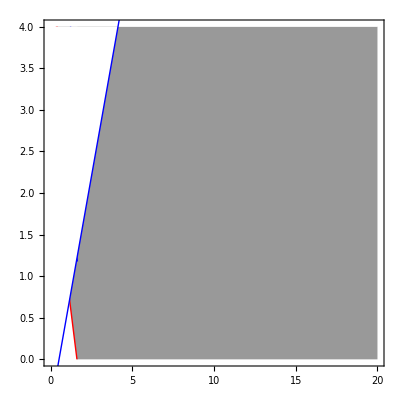

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Show[PlotRN20, PlotRN24,PlotRN22,PlotRP6,PlotRP12, PlotRP8, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,20},{0,4}},LabelStyle-> Larger]
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN20kaPN = plotPinvRN20/.kaPΝparsM;
PlotRN20 = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig20RΝM[x]<0&&AllFeas20M[x]]];

PinvRN24kaPN = plotPinvRN24/.kaPΝparsM;
PlotRN24 = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig24RΝM[x]<0&&AllFeas24M[x]]];

PinvRN22kaPN = plotPinvRN22/.kaPΝparsM;
PlotRN22 = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig22RΝM[x]<0&&AllFeas22M[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsM;
PlotRP6 = Plot[Νinv6kaPN,{k, 1.12,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

Νinv12kaPN = plotΝinv12/.kaPΝparsM;
PlotRP12 = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RPM[x]<0&&AllFeas12M[x]]];

Νinv8kaPN = plotΝinv8/.kaPΝparsM;
PlotRP8 = Plot[Νinv8kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RPM[x]<0&&AllFeas8M[x]]];
```

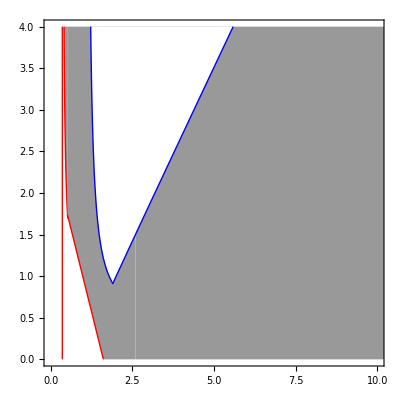

```mathematica
Show[PlotRN20, PlotRN24,PlotRN22,PlotRP6,PlotRP12, PlotRP8, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{0,4}},LabelStyle-> Larger]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN20kaPN = plotPinvRN20/.kaPΝparsL;
PlotRN20L = Plot[PinvRN20kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig20RΝL[x]<0&&AllFeas20L[x]]];

PinvRN24kaPN = plotPinvRN24/.kaPΝparsL;
PlotRN24L = Plot[PinvRN24kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig24RΝL[x]<0&&AllFeas24L[x]]];

PinvRN22kaPN = plotPinvRN22/.kaPΝparsL;
PlotRN22L = Plot[PinvRN22kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig22RΝL[x]<0&&AllFeas22L[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsL;
PlotRP6L = Plot[Νinv6kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPL[x]< 0&&AllFeas6L[x]]];

Νinv12kaPN = plotΝinv12/.kaPΝparsL;
PlotRP12L = Plot[Νinv12kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig12RPL[x]<0&&AllFeas12L[x]]];

Νinv8kaPN = plotΝinv8/.kaPΝparsL;
PlotRP8L = Plot[Νinv8kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RPL[x]<0&&AllFeas8L[x]]];
```

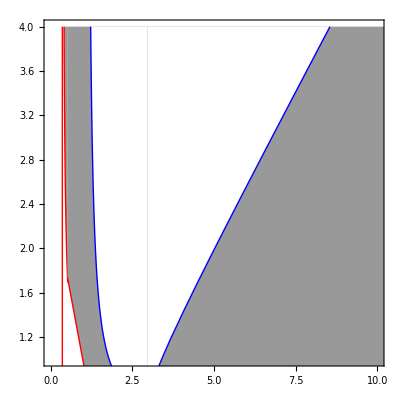

```mathematica
Show[PlotRN20L, PlotRN24L,PlotRN22L,PlotRP6L,PlotRP12L, PlotRP8L, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,10},{1,4}},LabelStyle-> Larger]
```

## Introduced Intermediate Consumer (Ν)

Define Model: suboptimal defense toward Ν

```mathematica
(* Modeling suboptimal defense -- Introduce ϕ the ratio of effeciency of introduced predator to recognized predator. As, ϕ goes to 1 defense against introduced pred is equally efficient. As it goes to zero defense effectiveness decreases. As efficiency shows up in the cost equations suboptimal response penalizes with NCEs as well  *)
```

```mathematica
Clear["Global`*"]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional reponse of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resourse *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fP ϕ)- aPR P (1 - eP fP ));
dΝdt = Ν (bΝR aΝR (1- eΝ fP ϕ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(*fitness is defined as the per capita growth rate of the resource*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - aΝR Ν (1- eΝ fP ϕ) -  aPR P (1 - eP fP);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))]
```

eΝ v (-aΝR (eΝ-1) fP Ν ϕ-aPR eP fP P+c0 r (eΝ+eP-1))

-eP v (aΝR eΝ fP Ν ϕ+aPR (eP-1) fP P-c0 r (eΝ+eP-1))

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1,k-> 5, c0->0.25, fP->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ϕ->1};
parsCoex = {r-> 1,k-> 5, c0->0.25, fP->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ϕ->1};
parsExc = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->1};
parsExcM = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->0.75};
parsExcL = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ϕ->0.45};

parsFacP = {r-> 1,k-> 0.7, c0->0.1, fP->0.8,  aPR-> 0.9, aPΝ -> .9, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.5, mP->0.5, mΝ->0.05, v-> 1, ϕ->1};
parsFacN = {r-> 1,k-> 0.28, c0->0.125, fP->0.8,  aPR-> 0.9, aPΝ -> 1.7, aΝR -> 0.8, bPΝ->0.5, bΝR->1, bPR->0.5, mP->0.35, mΝ->0.1, v-> 1, ϕ->1};
```

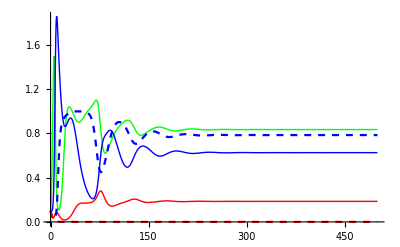

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsExc},{R,Ν, P, eΝ, eP},{t,0,500}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,500}, PlotStyle-> cols]
```

### Manipulate across gradients ϕ

```mathematica
parsϕExc = Delete[parsExc, 14]
```

{r→1,k→2.5,c0→0.4,fP→0.8,aPR→0.9,aPΝ→0.4,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1}

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsϕExc,{ϕ -> Φ}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{Φ,1,"ϕ"},0,1}]
```

ReplaceAll::reps: TraditionalForm`{Join[parsϕExc, {ϕ → 1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of TraditionalForm` in the first argument TraditionalForm`.

ReplaceAll::reps: TraditionalForm` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: TraditionalForm`{Join[parsϕExc, {ϕ → 1}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

#### Manipulate across gradient of k and others

```mathematica
parsϕkaPΝc0 = Delete[parsFacN, {{2}, {3},{6},{9},{11}, {14}}]
```

{r→1,fP→0.8,aPR→0.9,aΝR→0.8,bPΝ→0.5,bPR→0.5,mΝ→0.1,v→1}

```mathematica
{r-> 1,k-> 0.42, c0->0.125, fP->0.8,  aPR-> 0.9, aPΝ -> 1.7, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.5, mP->0.4, mΝ->0.05, v-> 1, ϕ->1};
```

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsϕkaPΝc0,{k -> κ, c0 -> χ, aPΝ -> α, ϕ -> Φ, bΝR-> β, mP-> μ}]},
{R,Ν, P, eΝ, eP},{t,0,500}]]],
{t,0,500},PlotRange->{0,All}, PlotStyle->cols],
{{κ,0.4,"k"},0,10}, {{χ,0.125,"c0"},0,1},{{α,1.7,"aPΝ"},0,2}, 
{{β,1,"bΝR"},0,1}, {{μ,.35,"mP"},0,1},{{Φ,1,"ϕ"},0,1}]
```

#### Comparison Plots

```mathematica
(*exclusion of P with increased novelty*)
```

```mathematica
parsExcPϕ = {r-> 1,k-> 2.5, c0->0.4, fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1};
```

```mathematica
finalϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsExcPϕ},{R,Ν, P, eΝ, eP},{t,0,1000}, {ϕ}];
```

```mathematica
Rfinalϕ = Plot[Evaluate[R[ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thick, Green}, 
PlotRange->{{0,1},{0,2}}];
Νfinalϕ = Plot[Evaluate[Ν[ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thick, Blue},  
PlotRange->{{0,1},{0,2}}];
Pfinalϕ = Plot[Evaluate[P[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle->  {Thick, Red},  
PlotRange->{{0,1},{0,2}}];
eΝfinalϕ = Plot[Evaluate[eΝ[ϕ][1000]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thick,Blue, Dashed}, 
PlotRange->{{0,1},{0,2}}];
ePfinalϕ = Plot[Evaluate[eP[ϕ][500]/.finalϕ,{ϕ,0,1}],PlotStyle-> {Thick, Red, Dashed}, 
PlotRange->{{0,1},{0,2}}];
```

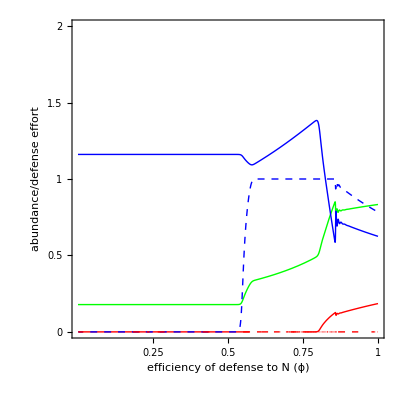

```mathematica
Show[Rfinalϕ,Νfinalϕ,Pfinalϕ,eΝfinalϕ, ePfinalϕ, Frame-> True, FrameLabel-> {"efficiency of defense to N (ϕ)","abundance/defense effort"}, 
AspectRatio -> 1/1, LabelStyle-> {Large, Black}, FrameTicks->{{{0,0.5,1, 1.5, 2},{None}},{{0.25, 0.5, 0.75, 1}, {None}}}]
```

```mathematica
(*coexistence via increased novelty*)
```

```mathematica
parsFacPϕ = Delete[parsFacN, 14]
```

{r→1,k→0.28,c0→0.125,fP→0.8,aPR→0.9,aPΝ→1.7,aΝR→0.8,bPΝ→0.5,bΝR→1,bPR→0.5,mP→0.35,mΝ→0.1,v→1}

```mathematica
finalFacϕ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsFacPϕ},{R,Ν, P, eΝ, eP},{t,0,1000}, {ϕ}];
```

```mathematica
RfinalϕFac = Plot[Evaluate[R[ϕ][1000]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thick, Green}, 
PlotRange->{{0.45,0.85},{0,0.8}}];
ΝfinalϕFac = Plot[Evaluate[Ν[ϕ][1000]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thick, Blue},  
PlotRange->{{0.45,0.85},{0,0.8}}];
PfinalϕFac = Plot[Evaluate[P[ϕ][1000]/.finalFacϕ,{ϕ,0,1}],PlotStyle->  {Thick, Red},  
PlotRange->{{0.45,0.85},{0,0.8}}];
eΝfinalϕFac = Plot[Evaluate[eΝ[ϕ][1000]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thick,Blue, Dashed}, 
PlotRange->{{0.45,0.85},{0,0.8}}];
ePfinalϕFac = Plot[Evaluate[eP[ϕ][1000]/.finalFacϕ,{ϕ,0,1}],PlotStyle-> {Thick, Red, Dashed}, 
PlotRange->{{0.45,0.85},{0,0.8}}];
```

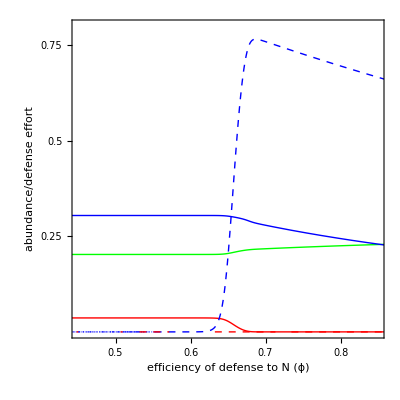

```mathematica
Show[RfinalϕFac,ΝfinalϕFac,PfinalϕFac,eΝfinalϕFac, ePfinalϕFac, Frame-> True, FrameLabel-> {"efficiency of defense to N (ϕ)","abundance/defense effort"}, 
AspectRatio -> 1/1, LabelStyle-> {Large, Black}, FrameTicks->{{{0.25, 0.5, 0.75},{None}},{{0.5, 0.6, 0.7, 0.8}, {None}}}]
```

Determine equilibria

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil//TableForm
```

R→0 | Ν→0 | P→0 | eP→1-eΝ | 
R→-(c0-1) k r | Ν→0 | P→0 | eP→1-eΝ | 
R→mP/(aPR bPR) | Ν→0 | P→(aPR r-mP/(bPR k))/aPR^2 | eΝ→0 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→-(aPR bPR (c0-1) k r+mP)/(aPR^2 bPR k) | eΝ→1 | eP→0
R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | P→(aPR bPR (c0-1) (fP-1) k r-mP)/(aPR^2 bPR (fP-1)^2 k) | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→mP/(aPR bPR fP k r-aPR bPR c0 fP k r)-1/fP+1 | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
R→(k r (fP-c0))/fP | Ν→0 | P→(c0 r)/(aPR fP) | eΝ→0 | eP→mP/(aPR bPR c0 k r-aPR bPR fP k r)+1/fP
R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
R→-(k (aΝR mP+aPΝ bPΝ (c0-1) r+aPR bPΝ (fP-1) mΝ))/(aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR k r (c0 (-fP)+c0+fP-1)+mP)-aPR (fP-1) k (aΝR bΝR mP+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bΝR bPΝ (c0-1) r+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | eΝ→0 | eP→1
R→(aPΝ c0 r+aPR fP mΝ)/(aΝR aPR bΝR fP) | Ν→(-aPΝ c0 r+aΝR aPR bΝR k r (fP-c0)-aPR fP mΝ)/(aΝR^2 aPR bΝR fP k) | P→(c0 r)/(aPR fP) | eΝ→0 | eP→(aPΝ r (aΝR aPR k (bΝR bPΝ (fP-c0)+bPR c0)-aPΝ bPΝ c0)+aPR fP (aΝR k (aPR bPR mΝ-aΝR bΝR mP)-aPΝ bPΝ mΝ))/(aΝR aPR bPR fP k (aPΝ c0 r+aPR fP mΝ))
R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→-(aΝR bΝR (c0-1) k r+mΝ)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→(aΝR r-mΝ/(bΝR k))/aΝR^2 | P→0 | eΝ→0 | eP→0
R→(k (aΝR mP (fP ϕ-1)+bPΝ (aPR mΝ-aPΝ (c0-1) r)))/(aPΝ bPΝ+aΝR aPR k (fP ϕ-1) (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR (c0-1) k r+mP)-aPR k (aΝR bΝR mP (fP ϕ-1)+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR k (fP ϕ-1) (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (fP ϕ-1) (aΝR bΝR mP (fP ϕ-1)-aPΝ bΝR bPΝ (c0-1) r+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR k (fP ϕ-1) (bPR-bΝR bPΝ))) | eΝ→1 | eP→0
R→mΝ/(aΝR bΝR-aΝR bΝR fP ϕ) | Ν→(aΝR bΝR (c0-1) k r (fP ϕ-1)-mΝ)/(aΝR^2 bΝR k (fP ϕ-1)^2) | P→0 | eΝ→1 | eP→0
R→-(k r (c0 ϕ+c0-fP ϕ))/(fP ϕ) | Ν→(c0 r)/(aΝR fP ϕ) | P→(c0 r)/(aPR fP) | eΝ→-(aPΝ c0 r ϕ+aPR (aΝR bΝR k r (c0 ϕ+c0-fP ϕ)+fP mΝ ϕ))/(aΝR aPR bΝR fP k r ϕ (fP ϕ-c0 (ϕ+1))) | eP→(aPΝ bPΝ c0 r-aΝR (aPR bPR k r (c0 ϕ+c0-fP ϕ)+fP mP ϕ))/(aΝR aPR bPR fP k r (fP ϕ-c0 (ϕ+1)))
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→(aΝR bΝR c0 k r-aΝR bΝR k r+mΝ)/(aΝR bΝR c0 fP k r ϕ-aΝR bΝR fP k r ϕ) | eP→(aΝR bΝR (c0-1) k r (fP ϕ-1)-mΝ)/(aΝR bΝR (c0-1) fP k r ϕ)
R→(k (ϕ (aΝR bΝR mP (-fP ϕ+ϕ+1)-aPΝ (c0-1) r (bPR-bΝR bPΝ))+aPR bPR mΝ (-fP ϕ+ϕ+1)))/(aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fP ϕ+ϕ+1)^2) | Ν→-(aΝR bΝR mP ϕ+aPR bPR (mΝ-aΝR bΝR (c0-1) k r ((fP-1) ϕ-1)))/(aΝR (aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fP ϕ+ϕ+1)^2)) | P→(ϕ (aPR bPR (aΝR bΝR (c0-1) k r ((fP-1) ϕ-1)-mΝ)-aΝR bΝR mP ϕ))/(aPR (aPΝ ϕ (bPR-bΝR bPΝ)+aΝR aPR bΝR bPR k (-fP ϕ+ϕ+1)^2)) | eΝ→(-aΝR aPΝ mP ϕ+aΝR aPR^2 bPR (fP-1) k mΝ ((fP-1) ϕ-1)+aPR (aΝR k (aΝR bΝR mP ((fP-1) ϕ-1)+aPΝ (c0-1) r (bPR (fP-1) ϕ-bΝR bPΝ))-aPΝ bPΝ mΝ))/(aΝR aPR fP k (ϕ (aΝR bΝR mP ((fP-1) ϕ-1)+aPΝ (c0-1) r (bPR-bΝR bPΝ))+aPR bPR mΝ ((fP-1) ϕ-1))) | eP→(aΝR aPΝ mP ϕ+aΝR aPR^2 bPR k mΝ ((fP-1) ϕ-1)+aPR (aΝR k (aΝR bΝR mP ((fP-1) ϕ-1) (fP ϕ-1)+aPΝ (c0-1) r (-bΝR bPΝ fP ϕ+bΝR bPΝ+bPR ϕ))+aPΝ bPΝ mΝ))/(aΝR aPR fP k (ϕ (aΝR bΝR mP ((fP-1) ϕ-1)+aPΝ (c0-1) r (bPR-bΝR bPΝ))+aPR bPR mΝ ((fP-1) ϕ-1)))
R→(aΝR fP mP ϕ-aPΝ bPΝ c0 r)/(aΝR aPR bPR fP ϕ) | Ν→(c0 r)/(aΝR fP ϕ) | P→(aPΝ bPΝ c0 r-aΝR (aPR bPR k r (c0-fP ϕ)+fP mP ϕ))/(aΝR aPR^2 bPR fP k ϕ) | eΝ→((aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))/(aΝR aPR fP k ϕ)+(bPR (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ c0 r-aΝR fP mP ϕ))/(bΝR bPΝ) | eP→0
R→k r (1-c0/(fP ϕ)) | Ν→(c0 r)/(aΝR fP ϕ) | P→0 | eΝ→mΝ/(aΝR bΝR c0 k r-aΝR bΝR fP k r ϕ)+1/(fP ϕ) | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
R→(k (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | P→(aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1 | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Detemine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aΝR eΝ fP Ν ϕ-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fP ϕ-1) | R (aΝR fP Ν ϕ-c0 r) | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aΝR bΝR Ν (1-eΝ fP ϕ) | aΝR bΝR R (1-eΝ fP ϕ)-aPΝ P-mΝ | -aΝR bΝR fP Ν R ϕ | -aPΝ Ν | 0
0 | -aΝR (eΝ-1) eΝ fP v ϕ | v (aΝR (1-2 eΝ) fP Ν ϕ-aPR eP fP P+c0 r (2 eΝ+eP-1)) | -aPR eΝ eP fP v | eΝ v (c0 r-aPR fP P)
aPR bPR P (1-eP fP) | aPΝ bPΝ P | 0 | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aΝR eΝ eP fP v ϕ | eP v (c0 r-aΝR fP Ν ϕ) | -aPR (eP-1) eP fP v | v (-aΝR eΝ fP Ν ϕ+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

(aΝR eΝ fP Ν ϕ-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fP ϕ-1) | R (aΝR fP Ν ϕ-c0 r)
aΝR bΝR Ν (1-eΝ fP ϕ) | aΝR bΝR R (1-eΝ fP ϕ)-aPΝ P-mΝ | -aΝR bΝR fP Ν R ϕ
0 | -aΝR (eΝ-1) eΝ fP v ϕ | v (aΝR (1-2 eΝ) fP Ν ϕ-aPR eP fP P+c0 r (2 eΝ+eP-1)))

(aΝR eΝ fP Ν ϕ-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aPR bPR P (1-eP fP) | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aPR (eP-1) eP fP v | v (-aΝR eΝ fP Ν ϕ+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subpars=Delete[parsExc,2];
subparsM=Delete[parsExcM,2];
subparsL=Delete[parsExcL,2];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq14RΝ=JRΝ/.equil[[14,All]]//FullSimplify;
Jeq21RΝ=JRΝ/.equil[[21,All]]//FullSimplify;
Jeq16RΝ=JRΝ/.equil[[16,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq3RP=JRP/.equil[[3,All]]//FullSimplify;
Jeq7RP=JRP/.equil[[7,All]]//FullSimplify;
Jeq5RP=JRP/.equil[[5,All]]//FullSimplify;
```

```mathematica
(* function to test if all abundances are greater than zero;used for region of feasibility. For plotting purposes, provides the region of "existence" but not "stability"*)
```

```mathematica
(* Coexistence*)
```

```mathematica
(* Jeq4=J/.equil[[4,All]]//FullSimplify;
Jeq5=J/.equil[[5,All]]//FullSimplify;
Jeq10=J/.equil[[10,All]]//FullSimplify;
Jeq12=J/.equil[[12,All]]//FullSimplify;
Jeq14=J/.equil[[14,All]]//FullSimplify;
Jeq15=J/.equil[[15,All]]//FullSimplify;
Jeq27=J/.equil[[27,All]]//FullSimplify; *)
```

```mathematica
AllFeas3[k_]=AllTrue[Re[equil[[3,All,2]]/.subpars],#≥0&];
AllFeas5[k_]=AllTrue[Re[equil[[5,All,2]]/.subpars],#≥0&];
AllFeas7[k_]=AllTrue[Re[equil[[7,All,2]]/.subpars],#≥0&];
AllFeas14[k_]=AllTrue[Re[equil[[14,All,2]]/.subpars],#≥0&];
AllFeas21[k_]=AllTrue[Re[equil[[21,All,2]]/.subpars],#≥0&];
AllFeas16[k_]=AllTrue[Re[equil[[16,All,2]]/.subpars],#≥0&];

AllFeas3M[k_]=AllTrue[Re[equil[[3,All,2]]/.subparsM],#≥0&];
AllFeas5M[k_]=AllTrue[Re[equil[[5,All,2]]/.subparsM],#≥0&];
AllFeas7M[k_]=AllTrue[Re[equil[[7,All,2]]/.subparsM],#≥0&];
AllFeas14M[k_]=AllTrue[Re[equil[[14,All,2]]/.subparsM],#≥0&];
AllFeas21M[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsM],#≥0&];
AllFeas16M[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsM],#≥0&];

AllFeas3L[k_]=AllTrue[Re[equil[[3,All,2]]/.subparsL],#≥0&];
AllFeas5L[k_]=AllTrue[Re[equil[[5,All,2]]/.subparsL],#≥0&];
AllFeas7L[k_]=AllTrue[Re[equil[[7,All,2]]/.subparsL],#≥0&];
AllFeas14L[k_]=AllTrue[Re[equil[[14,All,2]]/.subparsL],#≥0&];
AllFeas21L[k_]=AllTrue[Re[equil[[21,All,2]]/.subparsL],#≥0&];
AllFeas16L[k_]=AllTrue[Re[equil[[16,All,2]]/.subparsL],#≥0&];
```

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
(* RN system *)
```

```mathematica
pReEig14RΝ[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subpars]]]]; 
pReEig21RΝ[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subpars]]]];
pReEig16RΝ[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subpars]]]];

pReEig14RΝM[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsM]]]]; 
pReEig21RΝM[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsM]]]];
pReEig16RΝM[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsM]]]];

pReEig14RΝL[k_]=Max[Re[Eigenvalues[N[Jeq14RΝ/.subparsL]]]]; 
pReEig21RΝL[k_]=Max[Re[Eigenvalues[N[Jeq21RΝ/.subparsL]]]];
pReEig16RΝL[k_]=Max[Re[Eigenvalues[N[Jeq16RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig3RP[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subpars]]]];
pReEig7RP[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subpars]]]];
pReEig5RP[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subpars]]]];

pReEig3RPM[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsM]]]];
pReEig7RPM[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsM]]]];
pReEig5RPM[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsM]]]];

pReEig3RPL[k_]=Max[Re[Eigenvalues[N[Jeq3RP/.subparsL]]]];
pReEig7RPL[k_]=Max[Re[Eigenvalues[N[Jeq7RP/.subparsL]]]];
pReEig5RPL[k_]=Max[Re[Eigenvalues[N[Jeq5RP/.subparsL]]]];
```

```mathematica
(*Coexistence*)
```

```mathematica
(* pReEig4[ϕ_]=Max[Re[Eigenvalues[N[Jeq4/.parsϕ]]]];
pReEig5[ϕ_]=Max[Re[Eigenvalues[N[Jeq5/.parsϕ]]]];
pReEig10[ϕ_]=Max[Re[Eigenvalues[N[Jeq10/.parsϕ]]]];
pReEig12[ϕ_]=Max[Re[Eigenvalues[N[Jeq12/.parsϕ]]]];
pReEig14[ϕ_]=Max[Re[Eigenvalues[N[Jeq14/.parsϕ]]]];
pReEig15[ϕ_]=Max[Re[Eigenvalues[N[Jeq15/.parsϕ]]]];
pReEig27[ϕ_]=Max[Re[Eigenvalues[N[Jeq27/.parsϕ]]]]; *)
```

Produce Plots

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH = Delete[parsExc, {{2},{6}}];
kaPΝparsM = Delete[parsExcM, {{2},{6}}];
kaPΝparsL = Delete[parsExcL, {{2},{6}}];
```

#### new

```mathematica
RstarRN14 = equil[[14,1,2]]
NstarRN14= equil[[14,2,2]]
RstarRN21 = equil[[21,1,2]]
NstarRN21= equil[[21,2,2]];
RstarRN16 = equil[[16,1,2]];
NstarRN16= equil[[16,2,2]];
```

mΝ/(aΝR bΝR)

(aΝR r-mΝ/(bΝR k))/aΝR^2

k r (1-c0/(fP ϕ))

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN14 = bPR aPR (1 -0*fP)RstarRN14  + aPN bPΝ NstarRN14 - mP;
PinvRN21 = bPR aPR (1 -0*fP)RstarRN21  + aPN bPΝ NstarRN21 - mP;
PinvRN16 = bPR aPR (1 -0*fP)RstarRN16  + aPN bPΝ NstarRN16 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN14 = FullSimplify[Solve[PinvRN14==0,aPN]][[1,1,2]];
PinvRN14kaPN = plotPinvRN14/.kaPΝparsH;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig14RΝ[x]<0&&AllFeas14[x]]];

plotPinvRN21 = FullSimplify[Solve[PinvRN21==0,aPN]][[1,1,2]];
PinvRN21kaPN = plotPinvRN21/.kaPΝparsH;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝ[x]<0&&AllFeas21[x]]];

plotPinvRN16 = FullSimplify[Solve[PinvRN16==0,aPN]][[1,1,2]];
PinvRN16kaPN = plotPinvRN16/.kaPΝparsH;
PlotRN16 = Plot[PinvRN16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig16RΝ[x]<0&&AllFeas16[x]]];
```

#### Ν invades RP

```mathematica
Rstar3 = equil[[3,1,2]];
Pstar3= equil[[3,3,2]];
Rstar7 = equil[[7,1,2]];
Pstar7= equil[[7,3,2]];
Rstar5 = equil[[5,1,2]];
Pstar5= equil[[5,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv3 = bΝR aΝR (1 -0*fΝ)Rstar3  - aPΝ Pstar3 - mΝ;
Νinv7 = bΝR aΝR (1 -0*fΝ)Rstar7  - aPΝ Pstar7 - mΝ;
Νinv5= bΝR aΝR (1 -0*fΝ)Rstar5 - aPΝ Pstar5 - mΝ;
```

```mathematica
plotΝinv3= FullSimplify[Solve[Νinv3==0,aPΝ]][[1,1,2]];
Νinv3kaPN = plotΝinv3/.kaPΝparsH;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.1112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle->White, AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
RegionFunction->Function[{x},pReEig3RP[x]< 0&&AllFeas3[x]]];

plotΝinv7= FullSimplify[Solve[Νinv7==0,aPΝ]][[1,1,2]];
Νinv7kaPN = plotΝinv7/.kaPΝparsH;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RP[x]<0&&AllFeas7[x]]];

plotΝinv5= FullSimplify[Solve[Νinv5==0,aPΝ]][[1,1,2]];
Νinv5kaPN = plotΝinv5/.kaPΝparsH;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig5RP[x]<0&&AllFeas5[x]]];
```

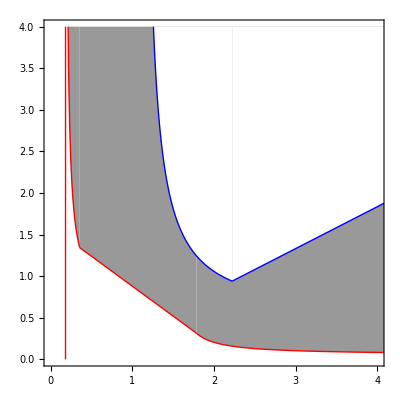

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,4},{0,4}},LabelStyle-> Larger]
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN14kaPN = plotPinvRN14/.kaPΝparsM;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig14RΝM[x]<0&&AllFeas14M[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsM;
PlotRN21 = Plot[PinvRN21kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝM[x]<0&&AllFeas21M[x]]];

PinvRN16kaPN = plotPinvRN16/.kaPΝparsM;
PlotRN16 = Plot[PinvRN16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig16RΝM[x]<0&&AllFeas16M[x]]];

Νinv3kaPN = plotΝinv3/.kaPΝparsM;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig3RPM[x]< 0&&AllFeas3M[x]]];

Νinv7kaPN = plotΝinv7/.kaPΝparsM;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RPM[x]<0&&AllFeas7M[x]]];

Νinv5kaPN = plotΝinv5/.kaPΝparsM;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig5RPM[x]<0&&AllFeas5M[x]]];
```

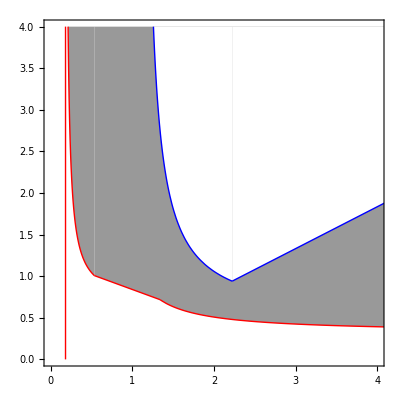

```mathematica
Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,4},{0,4}},LabelStyle-> Larger]
```

#### Low relative efficiency (ϕ = 0.5)

```mathematica
PinvRN14kaPN = plotPinvRN14/.kaPΝparsL;
PlotRN14 = Plot[PinvRN14kaPN,{k, 0,1.112}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig14RΝL[x]<0&&AllFeas14L[x]]];

PinvRN21kaPN = plotPinvRN21/.kaPΝparsL;
PlotRN21 = Plot[PinvRN21kaPN,{k, 1.113,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig21RΝL[x]<0&&AllFeas21L[x]]];

PinvRN16kaPN = plotPinvRN16/.kaPΝparsL;
PlotRN16 = Plot[PinvRN16kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig16RΝL[x]<0&&AllFeas16L[x]]];

Νinv3kaPN = plotΝinv3/.kaPΝparsL;
PlotRP3 = Plot[Νinv3kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},
Filling-> Top, FillingStyle->White,AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
RegionFunction->Function[{x},pReEig3RPL[x]< 0&&AllFeas3L[x]]];

Νinv7kaPN = plotΝinv7/.kaPΝparsL;
PlotRP7 = Plot[Νinv7kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig7RPL[x]<0&&AllFeas7L[x]]];

Νinv5kaPN = plotΝinv5/.kaPΝparsL;
PlotRP5 = Plot[Νinv5kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle->White,
RegionFunction->Function[{x},pReEig5RPL[x]<0&&AllFeas5L[x]]];
```

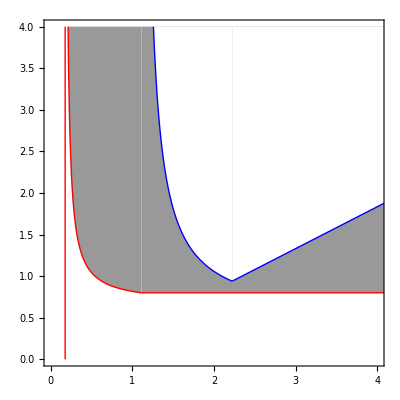

```mathematica
Show[PlotRN14, PlotRN21,PlotRN16,PlotRP3,PlotRP7, PlotRP5, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,4},{0,4}},LabelStyle-> Larger]
```

```mathematica
Show[%2261,ImageSize->Medium]
```

Define Model: naïveté to Ν

```mathematica
(* Modeling naïveté -- Introduce rho ρ which modifies the level of recognition of the predator by the basal resource by modifying the fitness equations. Now instead of the prey optimizing true per capita growth rate (true fitness) it will alter its level of effort to maximize "perceived fitness" based on a ρ-modified perception of the trophic-landscape.  Percived fitness alters the replicator equations (effort) which in turn affect the growth rates of the species. Effort shows up in the d equations so this modifies the effect of defense. Does not result in costly trait-modification because it does not show up in the cost equations no NCEs *)
```

```mathematica
Clear["Global`*"]
```

### Population Dynamics

(* d_i = (1 - e_i f_i); effect of defense on functional reponse of ith predator *)
(* c = (1 - c0 ∑_(i=N, P) e_i) cost of defense on growth rate of resourse *)

```mathematica
dRdt = R (r (1-c0 (eΝ + eP)) - R/k - aΝR Ν (1- eΝ fΝ)- aPR P (1 - eP fP));
dΝdt = Ν (bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ);
dPdt = P (bPR aPR (1 - eP fP) R+bPΝ aPΝ Ν - mP);
```

### Defense Effort and Fitness Dynamics

```mathematica
(* percieved fitness is defined as the per capita growth rate of the resource, but modified by a ρ parameter that varies from 1 (full recgnition) to zero (complete naïveté)*)
```

```mathematica
W = r (1-c0 (eΝ + eP))- R/k - ρ aΝR Ν (1- eΝ fΝ) - aPR P (1 - eP fP);
```

```mathematica
(* dynamic effort allocation to predator-specific defense *)
deΝdt=First@FullSimplify[ v eΝ(D[{W},eΝ]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
dePdt=First@FullSimplify[ v eP(D[{W},eP]-(eP D[{W},eP] + eΝ D[{W},eΝ]))];
```

```mathematica
sim={eΝ-> eΝ[t],eP-> eP[t],R-> R[t],Ν-> Ν[t],P-> P[t]};
```

Simulate dynamics to check if model is behaving

### Time-explicit equations for simulation across time

```mathematica
dR={R'[t] == First@{dRdt/.sim}, R[0]== 0.1};
dΝ = {Ν'[t]== First@{dΝdt/.sim}, Ν[0]== 0.1};
dP = {P'[t]== First@{dPdt/.sim}, P[0]== 0.1};
deΝ = {eΝ'[t]==First@{deΝdt/.sim},eΝ[0]== 0.1};
deP = {eP'[t]== First@{dePdt/.sim},eP[0]== 0.1};
```

### Plot time series

```mathematica
cols={{Thick,Green},{Thick,Blue},{Thick,Red},{Dashed,Blue},{Dashed, Red}};
```

```mathematica
pars = {r-> 1,k-> 5, c0->0.2, fP->0.5,fΝ->0.5,  aPR-> 0.25, aPΝ -> 1, aΝR -> 1, bPΝ->0.5, bΝR->0.5, bPR->0.5, mP->0.5, mΝ->0.5, v-> 1, ρ->.95};

parsCoex = {r-> 1,k-> 5, c0->0.25, fΝ->0.8, fP->0.8,  aPR-> 0.9, aPΝ -> 1.2, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.2, v-> 1, ρ->.95};
parsExc = {r-> 1,k-> 2.5, c0->0.4, fΝ->0.8,fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ρ->.95};
parsExcM = {r-> 1,k-> 2.5, c0->0.4, fΝ->0.8,fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ρ->0.75};
parsExcL = {r-> 1,k-> 2.5, c0->0.4, fΝ->0.8,fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1, ρ->0.5};

parsFacP = {r-> 1,k-> 0.7, c0->0.1, fP->0.8,  aPR-> 0.9, aPΝ -> .9, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.5, mP->0.5, mΝ->0.05, v-> 1, ρ->1};
```

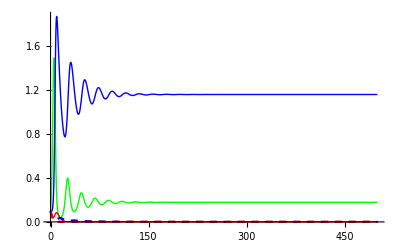

```mathematica
s=NDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsExcL},{R,Ν, P, eΝ, eP},{t,0,500}];
Plot[Evaluate[{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[s]], {t,0,500}, PlotStyle-> cols]
```

### Manipulate across gradients of ρ

```mathematica
parsExcρ = Delete[parsExc,15]
```

{r→1,k→2.5,c0→0.4,fΝ→0.8,fP→0.8,aPR→0.9,aPΝ→0.4,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1}

```mathematica
parsStabρ = {r-> 1,k-> 2.5, c0->0.4, fΝ->0.6,fP->0.5,  aPR-> 0.9, aPΝ -> .5, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.5, mP->0.5, mΝ->0.1, v-> 1};
```

```mathematica
Manipulate[
Plot[
Evaluate[
{R[t],Ν[t], P[t], eΝ[t], eP[t]}/.
First[NDSolve[{{dR,dΝ, dP,deΝ , deP}/.Join[parsStabρ,{ρ->Ρ}]},
{R,Ν, P, eΝ, eP},{t,0,1000}]]],
{t,0,1000},PlotRange->{0,All}, PlotStyle->cols],
{{Ρ,1,"ρ"},0,1}]
```

```mathematica
kparsρH = Delete[parsExc,2]
kparsρM = Delete[parsExcM,2]
kparsρL =Delete[parsExcL,2]
```

{r→1,c0→0.4,fΝ→0.8,fP→0.8,aPR→0.9,aPΝ→0.4,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1,ρ→0.95}

{r→1,c0→0.4,fΝ→0.8,fP→0.8,aPR→0.9,aPΝ→0.4,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1,ρ→0.75}

{r→1,c0→0.4,fΝ→0.8,fP→0.8,aPR→0.9,aPΝ→0.4,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1,ρ→0.5}

```mathematica
kfinalH=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρH},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalM=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρM },{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
kfinalL=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.kparsρL},{R,Ν, P, eΝ, eP},{t,0,1000}, {k}];
```

```mathematica
kfinalRH = Plot[Evaluate[R[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝH = Plot[Evaluate[Ν[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPH = Plot[Evaluate[P[k][500]/.kfinalH,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

$Aborted

```mathematica
kfinalRM = Plot[Evaluate[R[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝM = Plot[Evaluate[Ν[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPM = Plot[Evaluate[P[k][500]/.kfinalM,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

$Aborted

$Aborted

```mathematica
kfinalRL = Plot[Evaluate[R[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Green, 
PlotRange->{{0,10},{0,3}}];
kfinalΝL  = Plot[Evaluate[Ν[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Blue, 
PlotRange->{{0,10},{0,3}}];
kfinalPL  = Plot[Evaluate[P[k][500]/.kfinalL,{k,0,10}],PlotStyle-> Red, 
PlotRange->{{0,10},{0,3}}];
```

ParametricNDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of ParametricNDSolve :: ndode will be suppressed during this calculation.

ParametricNDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of ParametricNDSolve :: ndode will be suppressed during this calculation.

ParametricNDSolve::ndode: Input is not an ordinary differential equation.

General::stop: Further output of ParametricNDSolve :: ndode will be suppressed during this calculation.

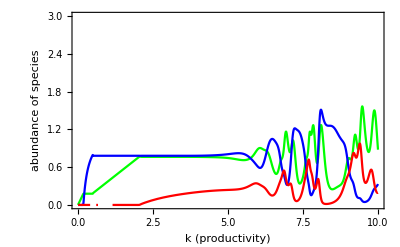

```mathematica
Show[kfinalRH,kfinalΝH,kfinalPH,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
LabelStyle-> {Larger, Black, Italic}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

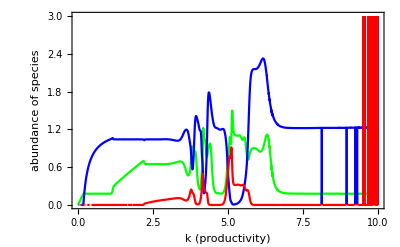

```mathematica
Show[kfinalRM,kfinalΝM, kfinalPM,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
LabelStyle-> {Larger, Black, Italic}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

```mathematica
Show[kfinalRL,kfinalΝL,kfinalPL,Frame-> True, FrameLabel-> {"k (productivity)","abundance of species"}, 
LabelStyle-> {Larger, Black, Italic}, PlotLegends->LineLegend[{Green,Blue,Red},{"R","Ν","P"}]]
```

-Graphics-

### Final densities of RNP across naivete towards N (ρ)

```mathematica
parsStabρplot = {r-> 1,k-> 2.5, c0->0.4, fΝ->.8,fP->0.8,  aPR-> 0.9, aPΝ -> .4, aΝR -> 0.8, bPΝ->0.5, bΝR->0.7, bPR->0.55, mP->0.5, mΝ->0.1, v-> 1};
parsFacPρ = {r-> 1,k-> 0.7, c0->0.1, fΝ->.8,fP->0.8,  aPR-> 0.9, aPΝ -> .9, aΝR -> 0.8, bPΝ->0.5, bΝR->0.9, bPR->0.5, mP->0.5, mΝ->0.05, v-> 1};
```

```mathematica
finalρ=ParametricNDSolve[{{dR,dΝ, dP, deΝ, deP}/.parsStabρplot},{R,Ν, P, eΝ, eP},{t,0,500}, {ρ}];
finalρR = Plot[Evaluate[R[ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thick, Green} ,
PlotRange->{{0,1},{0,2}}];
finalρΝ = Plot[Evaluate[Ν[ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thick, Blue}, 
PlotRange->{{0,1},{0,2}}];
finalρP = Plot[Evaluate[P[ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Thick, Red}, 
PlotRange->{{0,1},{0,2}}];
finalρeΝ = Plot[Evaluate[eΝ[ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Blue, Dashed}, 
PlotRange->{{0,1},{0,2}}];
finalρeP = Plot[Evaluate[eP[ρ][500]/.finalρ,{ρ,0,1}],PlotStyle-> {Red, Dashed}, 
PlotRange->{{0,1},{0,2}}];
```

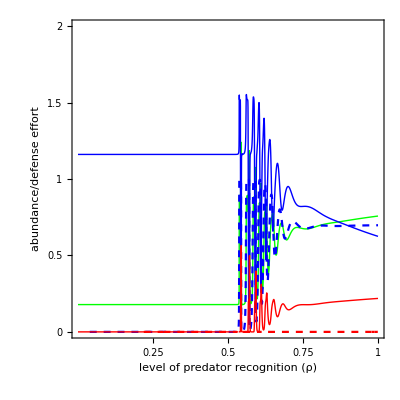

```mathematica
Show[finalρR,finalρΝ,finalρeΝ, finalρP, finalρeP, Frame-> True, FrameLabel-> {"level of predator recognition (ρ)","abundance/defense effort"}, 
AspectRatio -> 1/1, LabelStyle-> {Large, Black}, FrameTicks->{{{0,0.5,1, 1.5, 2},{None}},{{0.25, 0.5, 0.75, 1}, {None}}}]
```

Determine equilibria

```mathematica
equil=FullSimplify[Solve[{dRdt==0,dΝdt==0,dPdt==0, deΝdt == 0,dePdt==0},{R,Ν,P, eΝ, eP}]];
equil//TableForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

R→-(c0-1) k r | Ν→0 | P→0 | eP→1-eΝ | 
R→0 | Ν→0 | P→0 | eP→1-eΝ | 
R→k r | Ν→0 | P→0 | eΝ→0 | eP→0
R→(k (aΝR (fΝ-1) mP+bPΝ (aPR mΝ-aPΝ (c0-1) r)))/(aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR (c0-1) k r+mP)-aPR k (aΝR bΝR (fΝ-1) mP+aPR bPR mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | P→(aΝR (fΝ-1) k (-aΝR bΝR (fΝ-1) mP+aPΝ bΝR bPΝ (c0-1) r-aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR (fΝ-1) k (bPR-bΝR bPΝ))) | eΝ→1 | eP→0
R→(aΝR fΝ mP ρ-aPΝ bPΝ c0 r)/(aΝR aPR bPR fΝ ρ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→(-aPΝ^2 bΝR bPΝ^2 c0^2 r^2+aΝR fΝ ρ (aPR bPR k r (aΝR bΝR mP ρ (fΝ-c0)+aPR bPR c0 mΝ (ρ-1))-aΝR bΝR fΝ mP^2 ρ)+aΝR aPΝ bΝR bPΝ c0 ρ r (aPR bPR k r (c0-fΝ)+2 fΝ mP))/(aΝR aPR^2 bPR fΝ k ρ (aΝR bΝR fΝ mP ρ+aPΝ c0 r (-bΝR bPΝ+bPR (-ρ)+bPR))) | eΝ→(aΝR fΝ ρ (aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))-aPΝ c0 r (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)))/(aΝR aPR fΝ k (aΝR bΝR fΝ mP ρ+aPΝ c0 r (-bΝR bPΝ+bPR (-ρ)+bPR))) | eP→0
R→mP/(aPR bPR) | Ν→0 | P→(aPR r-mP/(bPR k))/aPR^2 | eΝ→0 | eP→0
R→mP/(aPR bPR) | Ν→0 | P→-(aPR bPR (c0-1) k r+mP)/(aPR^2 bPR k) | eΝ→1 | eP→0
R→mP/(aPR bPR-aPR bPR fP) | Ν→0 | P→(aPR bPR (c0-1) (fP-1) k r-mP)/(aPR^2 bPR (fP-1)^2 k) | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→mP/(aPR bPR fP k r-aPR bPR c0 fP k r)-1/fP+1 | eP→(1-mP/(aPR bPR k r-aPR bPR c0 k r))/fP
R→(k r (fP-c0))/fP | Ν→0 | P→(c0 r)/(aPR fP) | eΝ→0 | eP→mP/(aPR bPR c0 k r-aPR bPR fP k r)+1/fP
R→-(k (aΝR mP+aPΝ bPΝ (c0-1) r+aPR bPΝ (fP-1) mΝ))/(aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ)) | Ν→(aPΝ (aPR bPR k r (c0 (-fP)+c0+fP-1)+mP)-aPR (fP-1) k (aΝR bΝR mP+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | P→-(aPΝ bPΝ mΝ+aΝR k (aΝR bΝR mP+aPΝ bΝR bPΝ (c0-1) r+aPR bPR (fP-1) mΝ))/(aPΝ (aPΝ bPΝ+aΝR aPR (fP-1) k (bPR-bΝR bPΝ))) | eΝ→0 | eP→1
R→(aPΝ c0 r+aPR fP mΝ)/(aΝR aPR bΝR fP) | Ν→(-aPΝ c0 r+aΝR aPR bΝR k r (fP-c0)-aPR fP mΝ)/(aΝR^2 aPR bΝR fP k) | P→(c0 r)/(aPR fP) | eΝ→0 | eP→(aPΝ r (aΝR aPR k (bΝR bPΝ (fP-c0)+bPR c0)-aPΝ bPΝ c0)+aPR fP (aΝR k (aPR bPR mΝ-aΝR bΝR mP)-aPΝ bPΝ mΝ))/(aΝR aPR bPR fP k (aPΝ c0 r+aPR fP mΝ))
R→mΝ/(aΝR bΝR) | Ν→(aΝR r-mΝ/(bΝR k))/aΝR^2 | P→0 | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→1
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR) | Ν→-(aΝR bΝR (c0-1) k r+mΝ)/(aΝR^2 bΝR k) | P→0 | eΝ→0 | eP→1
R→mΝ/(aΝR bΝR-aΝR bΝR fΝ) | Ν→(aΝR bΝR (c0-1) (fΝ-1) k r-mΝ)/(aΝR^2 bΝR (fΝ-1)^2 k) | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→(1-mΝ/(aΝR bΝR k r-aΝR bΝR c0 k r))/fΝ | eP→mΝ/(aΝR bΝR fΝ k r-aΝR bΝR c0 fΝ k r)-1/fΝ+1
R→-(-(√k √r √(ρ (aΝR bΝR k r (c0-fΝ)^2+4 c0 fΝ mΝ)-4 c0 fΝ mΝ))/(√aΝR √bΝR √ρ)+c0 k r-fΝ k r)/(2 fΝ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→0 | eΝ→-((√ρ √(ρ (aΝR bΝR k r (c0-fΝ)^2+4 c0 fΝ mΝ)-4 c0 fΝ mΝ))/(√aΝR √bΝR √k √r)-c0 (ρ-2)-fΝ ρ)/(2 c0 fΝ (ρ-1)) | eP→0
R→-((√k √r √(ρ (aΝR bΝR k r (c0-fΝ)^2+4 c0 fΝ mΝ)-4 c0 fΝ mΝ))/(√aΝR √bΝR √ρ)+c0 k r-fΝ k r)/(2 fΝ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→0 | eΝ→((√ρ √(ρ (aΝR bΝR k r (c0-fΝ)^2+4 c0 fΝ mΝ)-4 c0 fΝ mΝ))/(√aΝR √bΝR √k √r)+c0 (ρ-2)+fΝ ρ)/(2 c0 fΝ (ρ-1)) | eP→0
R→(-aΝR aPR^2 bPR fP k mΝ ((fΝ-1) fP-fΝ) (bPΝ (bΝR-2 bΝR ρ)+bPR ρ)+(bΝR bPΝ-bPR ρ) √(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))+aΝR aPR fΝ k (aΝR bΝR mP ρ (fΝ (fP-1)-fP) (bΝR bPΝ+bPR (ρ-2))-aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)^2))/(2 aΝR aPR (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | Ν→(bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))-aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP ρ+aPR bPR fP mΝ))+aPΝ fΝ fP (bΝR bPΝ-bPR ρ) (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ))/(2 aΝR aPΝ fΝ (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | P→-(ρ (aPΝ fΝ fP (bΝR bPΝ-bPR ρ) (aΝR bΝR (aPR bPR (c0-1) k r (fΝ (fP-1)-fP)-2 fΝ mP)-2 aPR bPR fP mΝ)-bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))-aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP ρ+aPR bPR fP mΝ))))/(2 aPΝ aPR fP (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | eΝ→(aΝR aPR^2 bPR fP k mΝ (fΝ+2 fΝ (fP-1) ρ-(fΝ+1) fP)-√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ ρ-fP (fΝ ρ+ρ-2))+fP (aPΝ (c0-1) fΝ r (bΝR bPΝ-bPR ρ)+aPR bPR mΝ (-fΝ-2 fΝ (fP-1) ρ+fΝ fP+fP)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-aΝR aPΝ fΝ mP ρ+aΝR aPR^2 bPR (fP-1) k mΝ (fΝ (fP-1) ρ-fP)+aPR fP (-aΝR bΝR k (aΝR mP+aPΝ bPΝ (c0-1) r)-aPΝ bPΝ mΝ)+aΝR aPR fΝ (fP-1) k ρ (aΝR bΝR mP+aPΝ bPR (c0-1) r))))+aΝR aPR fΝ k (aΝR bΝR mP (fP (fΝ ρ+ρ-2)-fΝ ρ)-aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)) | eP→(aΝR aPR^2 bPR fP k mΝ (fΝ (2 ρ-1)-fΝ fP+fP)+√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ ρ-fP (fΝ ρ+ρ-2))+fP (aPΝ (c0-1) fΝ r (bΝR bPΝ-bPR ρ)+aPR bPR mΝ (-fΝ-2 fΝ (fP-1) ρ+fΝ fP+fP)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-aΝR aPΝ fΝ mP ρ+aΝR aPR^2 bPR (fP-1) k mΝ (fΝ (fP-1) ρ-fP)+aPR fP (-aΝR bΝR k (aΝR mP+aPΝ bPΝ (c0-1) r)-aPΝ bPΝ mΝ)+aΝR aPR fΝ (fP-1) k ρ (aΝR bΝR mP+aPΝ bPR (c0-1) r))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ ρ+(fΝ-1) fP (ρ-2))+aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))
R→(-aΝR aPR^2 bPR fP k mΝ ((fΝ-1) fP-fΝ) (bPΝ (bΝR-2 bΝR ρ)+bPR ρ)+(bPR ρ-bΝR bPΝ) √(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))+aΝR aPR fΝ k (aΝR bΝR mP ρ (fΝ (fP-1)-fP) (bΝR bPΝ+bPR (ρ-2))-aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)^2))/(2 aΝR aPR (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | Ν→(aPΝ fΝ fP (bΝR bPΝ-bPR ρ) (aΝR bΝR (2 fΝ mP-aPR bPR (c0-1) k r (fΝ (fP-1)-fP))+2 aPR bPR fP mΝ)-bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))+aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP ρ+aPR bPR fP mΝ)))/(2 aΝR aPΝ fΝ (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | P→-(ρ (bΝR bPR ((fΝ-1) fP-fΝ) (√(aΝR aPR k (4 aΝR^2 aPΝ bΝR fΝ^3 fP mP^2 (ρ-1) ρ+aΝR aPR^3 bPR^2 fP^2 k mΝ^2 (fΝ-fΝ fP+fP)^2+2 aPR^2 bPR fΝ fP mΝ (aΝR^2 bΝR k mP ρ (fΝ-fΝ fP+fP)^2+aPΝ fP (aΝR bΝR bPΝ (c0-1) k r (fΝ (fP-1)-fP)+ρ (aΝR (c0-1) k r (fΝ (fP-1)-fP) (bPR-2 bΝR bPΝ)+2 bPΝ fP mΝ)-2 bPΝ fP mΝ))+aΝR aPR fΝ^2 (aΝR^2 bΝR^2 k mP^2 ρ^2 (fΝ-fΝ fP+fP)^2+aPΝ^2 (c0-1)^2 fP^2 k r^2 (bΝR bPΝ-bPR ρ)^2-2 aPΝ fP mP (bPR ρ^2 (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP)-2 fP mΝ)+ρ (aΝR bΝR (c0-1) k r (fΝ (fP-1)-fP) (bΝR bPΝ-2 bPR)+2 fP mΝ (bPR-bΝR bPΝ))+2 bΝR bPΝ fP mΝ))))+aΝR aPR k ((fΝ-1) fP-fΝ) (aΝR bΝR fΝ mP ρ+aPR bPR fP mΝ))+aPΝ fΝ fP (bΝR bPΝ-bPR ρ) (aΝR bΝR (aPR bPR (c0-1) k r (fΝ (fP-1)-fP)-2 fΝ mP)-2 aPR bPR fP mΝ)))/(2 aPΝ aPR fP (aPΝ fΝ fP (bΝR bPΝ-bPR ρ)^2+aΝR aPR bΝR bPR k ρ (fΝ-fΝ fP+fP)^2 (bPR-bΝR bPΝ))) | eΝ→(aΝR aPR^2 bPR fP k mΝ (fΝ+2 fΝ (fP-1) ρ-(fΝ+1) fP)+√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ ρ-fP (fΝ ρ+ρ-2))+fP (aPΝ (c0-1) fΝ r (bΝR bPΝ-bPR ρ)+aPR bPR mΝ (-fΝ-2 fΝ (fP-1) ρ+fΝ fP+fP)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-aΝR aPΝ fΝ mP ρ+aΝR aPR^2 bPR (fP-1) k mΝ (fΝ (fP-1) ρ-fP)+aPR fP (-aΝR bΝR k (aΝR mP+aPΝ bPΝ (c0-1) r)-aPΝ bPΝ mΝ)+aΝR aPR fΝ (fP-1) k ρ (aΝR bΝR mP+aPΝ bPR (c0-1) r))))+aΝR aPR fΝ k (aΝR bΝR mP (fP (fΝ ρ+ρ-2)-fΝ ρ)-aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ)) | eP→(aΝR aPR^2 bPR fP k mΝ (fΝ (2 ρ-1)-fΝ fP+fP)-√(aΝR aPR k (aΝR aPR k (aΝR bΝR fΝ mP (fΝ ρ-fP (fΝ ρ+ρ-2))+fP (aPΝ (c0-1) fΝ r (bΝR bPΝ-bPR ρ)+aPR bPR mΝ (-fΝ-2 fΝ (fP-1) ρ+fΝ fP+fP)))^2-4 fΝ fP (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ) (-aΝR aPΝ fΝ mP ρ+aΝR aPR^2 bPR (fP-1) k mΝ (fΝ (fP-1) ρ-fP)+aPR fP (-aΝR bΝR k (aΝR mP+aPΝ bPΝ (c0-1) r)-aPΝ bPΝ mΝ)+aΝR aPR fΝ (fP-1) k ρ (aΝR bΝR mP+aPΝ bPR (c0-1) r))))+aΝR aPR fΝ k (aΝR bΝR mP (fΝ ρ+(fΝ-1) fP (ρ-2))+aPΝ (c0-1) fP r (bΝR bPΝ-bPR ρ)))/(2 aΝR aPR fΝ fP k (ρ-1) (aΝR bΝR fΝ mP+aPR bPR fP mΝ))
R→(√(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ))-aΝR aPR bΝR fΝ k ρ r (c0 (fΝ+fP)-fΝ fP))/(2 aΝR aPR bΝR fΝ^2 fP ρ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→(c0 r)/(aPR fP) | eΝ→(aΝR aPR bΝR fΝ k r (c0 (fP (ρ-2)-fΝ ρ)+fΝ fP ρ)-√(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ)))/(2 aΝR aPR bΝR c0 fΝ^2 fP k (ρ-1) r) | eP→(2 aΝR aPR^2 bPR c0 fΝ^2 fP k mΝ (ρ-1) ρ r+(aPΝ bPΝ c0 r-aΝR fΝ mP ρ) √(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ))+aΝR aPR fΝ k ρ r (aPΝ c0 r (bΝR bPΝ (c0 (fΝ+fP)-fΝ fP)+2 bPR c0 fΝ (ρ-1))-aΝR bΝR fΝ mP ρ (c0 (fΝ+fP)-fΝ fP)))/(2 aΝR aPR bPR c0 fΝ^2 fP k (ρ-1) ρ r (aPΝ c0 r+aPR fP mΝ))
R→-(aΝR aPR bΝR fΝ k ρ r (c0 (fΝ+fP)-fΝ fP)+√(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ)))/(2 aΝR aPR bΝR fΝ^2 fP ρ) | Ν→(c0 r)/(aΝR fΝ ρ) | P→(c0 r)/(aPR fP) | eΝ→(aΝR aPR bΝR fΝ k r (c0 (fP (ρ-2)-fΝ ρ)+fΝ fP ρ)+√(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ)))/(2 aΝR aPR bΝR c0 fΝ^2 fP k (ρ-1) r) | eP→(2 aΝR aPR^2 bPR c0 fΝ^2 fP k mΝ (ρ-1) ρ r+(aΝR fΝ mP ρ-aPΝ bPΝ c0 r) √(aΝR aPR bΝR fΝ^2 k ρ r (4 aPΝ c0^2 fΝ fP (ρ-1) r+aPR ρ (aΝR bΝR k r (fΝ fP-c0 (fΝ+fP))^2+4 c0 fΝ fP^2 mΝ)-4 aPR c0 fΝ fP^2 mΝ))+aΝR aPR fΝ k ρ r (aPΝ c0 r (bΝR bPΝ (c0 (fΝ+fP)-fΝ fP)+2 bPR c0 fΝ (ρ-1))-aΝR bΝR fΝ mP ρ (c0 (fΝ+fP)-fΝ fP)))/(2 aΝR aPR bPR c0 fΝ^2 fP k (ρ-1) ρ r (aPΝ c0 r+aPR fP mΝ))
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→1 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→0
R→0 | Ν→mP/(aPΝ bPΝ) | P→-mΝ/aPΝ | eΝ→0 | eP→1
R→(k (-aΝR mP+aPΝ bPΝ r+aPR bPΝ mΝ))/(aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR)) | Ν→(aPR k (aΝR bΝR mP-aPR bPR mΝ)+aPΝ (mP-aPR bPR k r))/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | P→(aΝR k (-aΝR bΝR mP+aPΝ bΝR bPΝ r+aPR bPR mΝ)-aPΝ bPΝ mΝ)/(aPΝ (aPΝ bPΝ+aΝR aPR k (bΝR bPΝ-bPR))) | eΝ→0 | eP→0
R→0 | Ν→0 | P→0 | eΝ→1 | eP→0
R→-(c0-1) k r | Ν→0 | P→0 | eΝ→1 | eP→0
R→0 | Ν→0 | P→0 | eΝ→0 | eP→0

Detemine Jacobian and substitute equilibria

### Determine Jacobian

```mathematica
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
J= JacobianMatrix[{dRdt,dΝdt,deΝdt, dPdt, dePdt},{R,Ν,eΝ,P, eP}]//FullSimplify;
JRΝ= JacobianMatrix[{dRdt,dΝdt,deΝdt},{R,Ν,eΝ}]//FullSimplify;
JRP= JacobianMatrix[{dRdt,dPdt, dePdt},{R,P, eP}]//FullSimplify;
J//MatrixForm
JRΝ//MatrixForm
JRP//MatrixForm
```

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fΝ-1) | R (aΝR fΝ Ν-c0 r) | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aΝR bΝR Ν (1-eΝ fΝ) | aΝR bΝR R (1-eΝ fΝ)-aPΝ P-mΝ | -aΝR bΝR fΝ Ν R | -aPΝ Ν | 0
0 | -aΝR (eΝ-1) eΝ fΝ ρ v | v (aΝR (1-2 eΝ) fΝ Ν ρ-aPR eP fP P+c0 r (2 eΝ+eP-1)) | -aPR eΝ eP fP v | eΝ v (c0 r-aPR fP P)
aPR bPR P (1-eP fP) | aPΝ bPΝ P | 0 | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aΝR eΝ eP fΝ ρ v | eP v (c0 r-aΝR fΝ Ν ρ) | -aPR (eP-1) eP fP v | v (-aΝR eΝ fΝ Ν ρ+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aΝR R (eΝ fΝ-1) | R (aΝR fΝ Ν-c0 r)
aΝR bΝR Ν (1-eΝ fΝ) | aΝR bΝR R (1-eΝ fΝ)-aPΝ P-mΝ | -aΝR bΝR fΝ Ν R
0 | -aΝR (eΝ-1) eΝ fΝ ρ v | v (aΝR (1-2 eΝ) fΝ Ν ρ-aPR eP fP P+c0 r (2 eΝ+eP-1)))

(aΝR eΝ fΝ Ν-aΝR Ν+aPR P (eP fP-1)-c0 r (eΝ+eP)-(2 R)/k+r | aPR R (eP fP-1) | R (aPR fP P-c0 r)
aPR bPR P (1-eP fP) | aPΝ bPΝ Ν+aPR bPR R (1-eP fP)-mP | -aPR bPR fP P R
0 | -aPR (eP-1) eP fP v | v (-aΝR eΝ fΝ Ν ρ+aPR (1-2 eP) fP P+c0 r (eΝ+2 eP-1)))

### Functions for working with equilibrium values across a gradient of productivity (k)

```mathematica
subpars=Delete[parsExc,2];
subparsM=Delete[parsExcM,2];
subparsL=Delete[parsExcL,2];
```

```mathematica
(*RN system*)
```

```mathematica
Jeq13RΝ=JRΝ/.equil[[13,All]]//FullSimplify;
Jeq19RΝ=JRΝ/.equil[[19,All]]//FullSimplify;
Jeq17RΝ=JRΝ/.equil[[17,All]]//FullSimplify;
```

```mathematica
(*RP system*)
```

```mathematica
Jeq6RP=JRP/.equil[[6,All]]//FullSimplify;
Jeq10RP=JRP/.equil[[10,All]]//FullSimplify;
Jeq8RP=JRP/.equil[[8,All]]//FullSimplify;
```

```mathematica
AllFeas6[k_]=AllTrue[Re[equil[[6,All,2]]/.subpars],#≥0&];
AllFeas8[k_]=AllTrue[Re[equil[[8,All,2]]/.subpars],#≥0&];
AllFeas10[k_]=AllTrue[Re[equil[[10,All,2]]/.subpars],#≥0&];
AllFeas13[k_]=AllTrue[Re[equil[[13,All,2]]/.subpars],#≥0&];
AllFeas17[k_]=AllTrue[Re[equil[[17,All,2]]/.subpars],#≥0&];
AllFeas19[k_]=AllTrue[Re[equil[[19,All,2]]/.subpars],#≥0&];

AllFeas6M[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsM],#≥0&];
AllFeas8M[k_]=AllTrue[Re[equil[[8,All,2]]/.subparsM],#≥0&];
AllFeas10M[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsM],#≥0&];
AllFeas13M[k_]=AllTrue[Re[equil[[13,All,2]]/.subparsM],#≥0&];
AllFeas17M[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsM],#≥0&];
AllFeas19M[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsM],#≥0&];

AllFeas6L[k_]=AllTrue[Re[equil[[6,All,2]]/.subparsL],#≥0&];
AllFeas8L[k_]=AllTrue[Re[equil[[8,All,2]]/.subparsL],#≥0&];
AllFeas10L[k_]=AllTrue[Re[equil[[10,All,2]]/.subparsL],#≥0&];
AllFeas13L[k_]=AllTrue[Re[equil[[13,All,2]]/.subparsL],#≥0&];
AllFeas17L[k_]=AllTrue[Re[equil[[17,All,2]]/.subparsL],#≥0&];
AllFeas19L[k_]=AllTrue[Re[equil[[19,All,2]]/.subparsL],#≥0&];
```

```mathematica
(* function to give dominant eigenvalues for a given equilibium at a given level of k and IGP level*)
```

```mathematica
(* RN system *)
```

```mathematica
pReEig19RΝ[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subpars]]]];pReEig17RΝ[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subpars]]]];pReEig13RΝ[k_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subpars]]]];

pReEig13RΝM[k_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsM]]]];
pReEig19RΝM[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsM]]]];
pReEig17RΝM[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsM]]]];

pReEig13RΝL[k_]=Max[Re[Eigenvalues[N[Jeq13RΝ/.subparsL]]]] ;
pReEig19RΝL[k_]=Max[Re[Eigenvalues[N[Jeq19RΝ/.subparsL]]]];
pReEig17RΝL[k_]=Max[Re[Eigenvalues[N[Jeq17RΝ/.subparsL]]]];
```

```mathematica
(*RP system*)
```

```mathematica
pReEig6RP[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subpars]]]];
pReEig10RP[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subpars]]]];
pReEig8RP[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subpars]]]];

pReEig6RPM[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsM]]]];
pReEig10RPM[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsM]]]];
pReEig8RPM[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsM]]]];

pReEig6RPL[k_]=Max[Re[Eigenvalues[N[Jeq6RP/.subparsL]]]];
pReEig10RPL[k_]=Max[Re[Eigenvalues[N[Jeq10RP/.subparsL]]]];
pReEig8RPL[k_]=Max[Re[Eigenvalues[N[Jeq8RP/.subparsL]]]];
```

Produce plots

### Invasibility Plot (k and aPN)

#### P invades RN

```mathematica
kaPΝparsH = Delete[parsExc, {{2},{7}}]
kaPΝparsM = Delete[parsExcM, {{2},{7}}]
kaPΝparsL = Delete[parsExcL, {{2},{7}}]
```

{r→1,c0→0.4,fΝ→0.8,fP→0.8,aPR→0.9,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1,ρ→0.95}

{r→1,c0→0.4,fΝ→0.8,fP→0.8,aPR→0.9,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1,ρ→0.75}

{r→1,c0→0.4,fΝ→0.8,fP→0.8,aPR→0.9,aΝR→0.8,bPΝ→0.5,bΝR→0.7,bPR→0.5,mP→0.5,mΝ→0.1,v→1,ρ→0.5}

#### new

```mathematica
RstarRN13 = equil[[13,1,2]];
NstarRN13= equil[[13,2,2]];
RstarRN19 = equil[[19,1,2]];
NstarRN19= equil[[19,2,2]];
RstarRN17 = equil[[17,1,2]];
NstarRN17= equil[[17,2,2]];
```

```mathematica
(*equilibria for the RΝ system *)
```

```mathematica
PinvRN13 = bPR aPR (1 -0*fP)RstarRN13  + aPN bPΝ NstarRN13 - mP;
PinvRN19 = bPR aPR (1 -0*fP)RstarRN19  + aPN bPΝ NstarRN19 - mP;
PinvRN17 = bPR aPR (1 -0*fP)RstarRN17  + aPN bPΝ NstarRN17 - mP;
```

```mathematica
(*Per capita growth equation for P at above equilibrium (when positive, P invades). Note: eP = 0 when P is absent so effect on P term goes to 1*)
```

#### P invades RΝ

```mathematica
plotPinvRN13 = FullSimplify[Solve[PinvRN13==0,aPN]][[1,1,2]];
PinvRN13kaPN = plotPinvRN13/.kaPΝparsH;
PlotRN13 = Plot[PinvRN13kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig13RΝ[x]<0&&AllFeas13[x]]];

plotPinvRN19 = FullSimplify[Solve[PinvRN19==0,aPN]][[1,1,2]];
PinvRN19kaPN = plotPinvRN19/.kaPΝparsH;
PlotRN19 = Plot[PinvRN19kaPN,{k, 0,2.45}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig19RΝ[x]<0&&AllFeas19[x]]];

plotPinvRN17 = FullSimplify[Solve[PinvRN17==0,aPN]][[1,1,2]];
PinvRN17kaPN = plotPinvRN17/.kaPΝparsH;
PlotRN17 = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝ[x]<0&&AllFeas17[x]]];
```

#### Ν invades RP

```mathematica
Rstar6 = equil[[6,1,2]];
Pstar6= equil[[6,3,2]];
Rstar10 = equil[[10,1,2]];
Pstar10= equil[[10,3,2]];
Rstar8 = equil[[8,1,2]];
Pstar8= equil[[8,3,2]];
```

```mathematica
(*bΝR aΝR (1- eΝ fΝ) R- aPΝ P - mΝ*)
```

```mathematica
Νinv6 = bΝR aΝR (1 -0*fΝ)Rstar6  - aPΝ Pstar6 - mΝ;
Νinv10 = bΝR aΝR (1 -0*fΝ)Rstar10  - aPΝ Pstar10 - mΝ;
Νinv8= bΝR aΝR (1 -0*fΝ)Rstar8 - aPΝ Pstar8 - mΝ;
```

```mathematica
plotΝinv6= FullSimplify[Solve[Νinv6==0,aPΝ]][[1,1,2]];
Νinv6kaPN = plotΝinv6/.kaPΝparsH;
PlotRP6 = Plot[Νinv6kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RP[x]< 0&&AllFeas6[x]]];

plotΝinv10= FullSimplify[Solve[Νinv10==0,aPΝ]][[1,1,2]];
Νinv10kaPN = plotΝinv10/.kaPΝparsH;
PlotRP10 = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RP[x]<0&&AllFeas10[x]]];

plotΝinv8= FullSimplify[Solve[Νinv8==0,aPΝ]][[1,1,2]];
Νinv8kaPN = plotΝinv8/.kaPΝparsH;
PlotRP8 = Plot[Νinv8kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RP[x]<0&&AllFeas8[x]]];
```

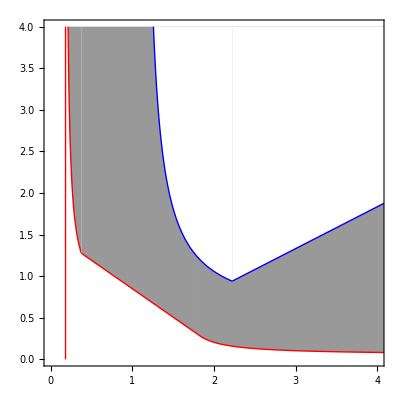

```mathematica
(* This replicates the domains of coexistence lines in Nakazawa Fig. 2a far left except...because the vertical lines are exactly on bounday of stability? *)
Show[PlotRN13, PlotRN19,PlotRN17,PlotRP6,PlotRP10, PlotRP8, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,4},{0,4}},LabelStyle-> Larger]
```

#### Medium relative efficiency (ϕ = 0.75)

```mathematica
PinvRN13kaPN = plotPinvRN13/.kaPΝparsM;
PlotRN13M = Plot[PinvRN13kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig13RΝM[x]<0&&AllFeas13M[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsM;
PlotRN19M = Plot[PinvRN19kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig19RΝM[x]<0&&AllFeas19M[x]]];

PinvRN17kaPN = plotPinvRN17/.kaPΝparsM;
PlotRN17M = Plot[PinvRN17kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝM[x]<0&&AllFeas17M[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsM;
PlotRP6M = Plot[Νinv6kaPN,{k, 1.112,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig6RPM[x]< 0&&AllFeas6M[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsM;
PlotRP10M = Plot[Νinv10kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig10RPM[x]<0&&AllFeas10M[x]]];

Νinv8kaPN = plotΝinv8/.kaPΝparsM;
PlotRP8M = Plot[Νinv8kaPN,{k, 0,20}, PlotRange->{{0,20},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RPM[x]<0&&AllFeas8M[x]]];
```

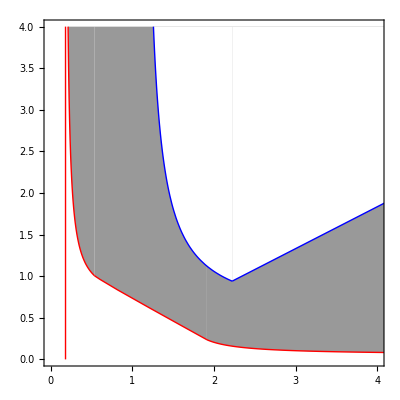

```mathematica
Show[PlotRN13M, PlotRN19M,PlotRN17M,PlotRP6M,PlotRP10M, PlotRP8M, Frame->True, AspectRatio -> 1/1, PlotRange->{{0,4},{0,4}},LabelStyle-> Larger]
```

#### Low relative efficiency (ϕ = 0.5)

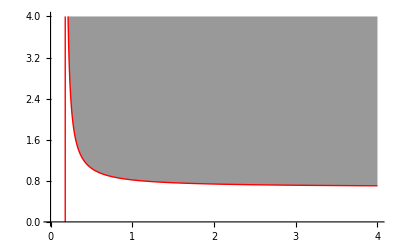

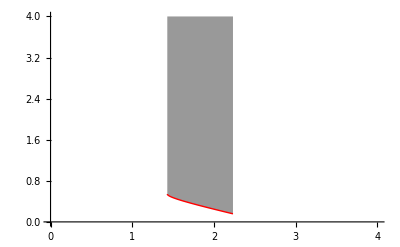

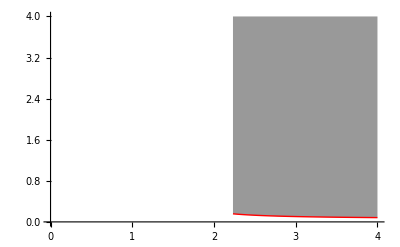

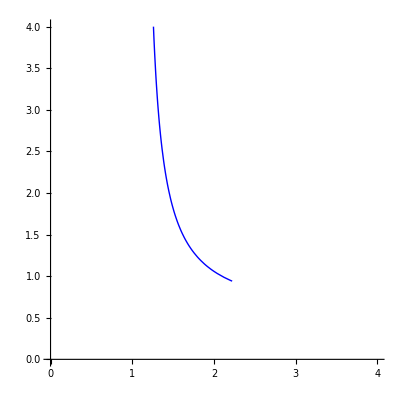

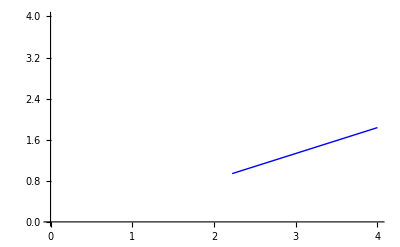

-Graphics-

```mathematica
PinvRN13kaPN = plotPinvRN13/.kaPΝparsL;
PlotRN13L = Plot[PinvRN13kaPN,{k, 0,4},  PlotRange->{{0,4},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6],
RegionFunction->Function[{x},pReEig13RΝL[x]<0&&AllFeas13L[x]]];

PinvRN19kaPN = plotPinvRN19/.kaPΝparsL;
PlotRN19L = Plot[PinvRN19kaPN,{k, 0,4}, PlotRange->{{0,4},{0,4}} ,PlotStyle->{Red, Thick},
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig19RΝL[x]<0&&AllFeas19L[x]]];

PinvRN17kaPN = plotPinvRN17/.kaPΝparsL;
PlotRN17L = Plot[PinvRN17kaPN,{k, 0,4}, PlotRange->{{0,4},{0,4}} ,PlotStyle->{Red, Thick}, 
Filling-> Top, FillingStyle-> GrayLevel[0.6], 
RegionFunction->Function[{x},pReEig17RΝL[x]<0&&AllFeas17L[x]]];

Νinv6kaPN = plotΝinv6/.kaPΝparsL;
PlotRP6L = Plot[Νinv6kaPN,{k, 0,4}, PlotRange->{{0,4},{0,4}} ,PlotStyle->{Blue, Thick},AspectRatio -> 1/1,LabelStyle-> {Larger, Black},
Filling-> Top, FillingStyle-> White, 
RegionFunction->Function[{x},pReEig6RPL[x]<0&&AllFeas6L[x]]];

Νinv10kaPN = plotΝinv10/.kaPΝparsL;
PlotRP10L = Plot[Νinv10kaPN,{k, 0,4}, PlotRange->{{0,4},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,
RegionFunction->Function[{x},pReEig10RPL[x]<0&&AllFeas10L[x]]];

Νinv8kaPN = plotΝinv8/.kaPΝparsL;
PlotRP8L = Plot[Νinv8kaPN,{k, 0,4}, PlotRange->{{0,4},{0,4}} ,PlotStyle->{Blue, Thick}, 
Filling-> Top, FillingStyle-> White,  
RegionFunction->Function[{x},pReEig8RPL[x]<0&&AllFeas8L[x]]];
```

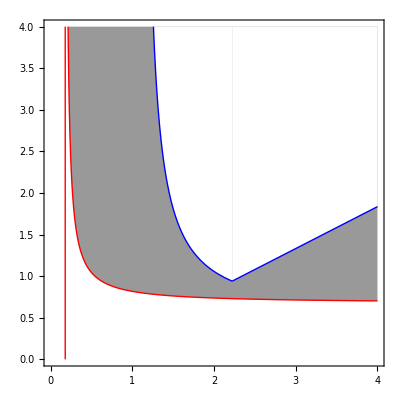

```mathematica
Show[PlotRN13L, PlotRP6L,PlotRP10L, PlotRP8L,Frame->True, AspectRatio -> 1/1, PlotRange->{{0,4},{0,4}},LabelStyle-> Larger]
```